```mathematica
ProgressIndicator[Dynamic[i],{1,n}]
```

```mathematica
ProgressIndicator[Dynamic[j],{i,n}]
```

ProgressIndicator[,{i,100}]

## Definitions

```mathematica
umin=0;
umax=1000;
n=200;
h=umax/n;
vmin=10^-5;
vmax=200;
vc=5;
vl=2;
μ=0.1;
qB=0.05;
```

# GR WAVE - temporal evolution m=0

## Definitions

```mathematica
f[r_]=1-2/r;V[r_,l_]=f[r]((l(l+1))/r^2+f'[r]/r+μ^2);
fr[rs_]:=Which[TrueQ[rs≥-150],x/.FindRoot[rs==x+2Log[Abs[x/2-1]],{x,2*(1+10^-40),2000},Method->"Secant",WorkingPrecision->64],TrueQ[rs<150],2*(1+10^-40)];frs[r_]=r+2Log[Abs[r/2-1]];
```

## Calculations

Initialization

```mathematica
Do[
v=vmin+j*h;
Y[0,j]=N[Exp[-10^1(v-vc)^2],64];
If[TrueQ[Abs[Y[0,j]]<10^-64],Y[0,j]=0];
Y[j,j]=0;
,{j,0,n}];
Do[
u=umin+i*h;
Do[
v=vmin+j*h;
rrs=(v-u)/2;
rr=fr[rrs];
YS=Y[i-1,j-1];
YE=Y[i-1,j];
YW=Y[i,j-1];
VS=V[rr,vl];
Y[i,j]=(YE+YW)*(16-h^2*VS)/(16+h^2*VS)-YS;
,{j,i+1,n}];
,{i,1,n}]
rs=5;
data1={};
Do[
v=vmin+i*h;
u=v-2*rs;
iu=Round[(u-umin)/h];
iv=Round[(v-vmin)/h];
If[TrueQ[(iu≥0&&iu<n)&&(iv≥0&&iv<n)],t=0.5*(u+v);
data1=Append[data1,{t,Y[iu,iv]}]
];
,{i,0,n}]
```

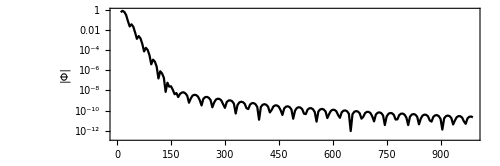

```mathematica
P1=ListLogPlot[Abs[data1],Joined->True,Frame->True,PlotRange->All,PlotStyle->{Black},BaseStyle->{14,FontFamily->"Times"},FrameLabel->{"t","|Φ|"},ImageSize->500,AspectRatio->1/3]
```

# GR WAVE - temporal evolution m=1

## Definitions

```mathematica
m=1;
f[r_]=1-2/r;V[r_,l_]=f[r]((l(l+1))/r^2+f'[r]/r+μ^2-m qB );
fr[rs_]:=Which[TrueQ[rs≥-150],x/.FindRoot[rs==x+2Log[Abs[x/2-1]],{x,2*(1+10^-40),2000},Method->"Secant",WorkingPrecision->64],TrueQ[rs<150],2*(1+10^-40)];frs[r_]=r+2Log[Abs[r/2-1]];
```

## Calculations

Initialization

```mathematica
Do[
v=vmin+j*h;
Y[0,j]=N[Exp[-10^1(v-vc)^2],64];
If[TrueQ[Abs[Y[0,j]]<10^-64],Y[0,j]=0];
Y[j,j]=0;
,{j,0,n}];
Do[
u=umin+i*h;
Do[
v=vmin+j*h;
rrs=(v-u)/2;
rr=fr[rrs];
YS=Y[i-1,j-1];
YE=Y[i-1,j];
YW=Y[i,j-1];
VS=V[rr,vl];
Y[i,j]=(YE+YW)*(16-h^2*VS)/(16+h^2*VS)-YS;
,{j,i+1,n}];
,{i,1,n}]
rs=5;
data2={};
Do[
v=vmin+i*h;
u=v-2*rs;
iu=Round[(u-umin)/h];
iv=Round[(v-vmin)/h];
If[TrueQ[(iu≥0&&iu<n)&&(iv≥0&&iv<n)],t=0.5*(u+v);
data2=Append[data2,{t,Y[iu,iv]}]
];
,{i,0,n}]
```

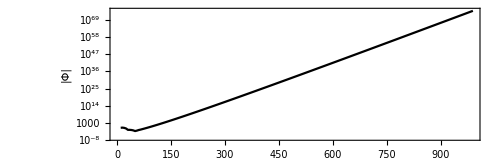

```mathematica
P2=ListLogPlot[Abs[data2],Joined->True,Frame->True,PlotRange->All,PlotStyle->{Black},BaseStyle->{14,FontFamily->"Times"},FrameLabel->{"t","|Φ|"},ImageSize->500,AspectRatio->1/3]
```

# GR WAVE - temporal evolution m=-1

## Definitions

```mathematica
m=-1;
f[r_]=1-2/r;V[r_,l_]=f[r]((l(l+1))/r^2+f'[r]/r+μ^2-m qB );
fr[rs_]:=Which[TrueQ[rs≥-150],x/.FindRoot[rs==x+2Log[Abs[x/2-1]],{x,2*(1+10^-40),2000},Method->"Secant",WorkingPrecision->64],TrueQ[rs<150],2*(1+10^-40)];frs[r_]=r+2Log[Abs[r/2-1]];
```

## Calculations

Initialization

```mathematica
Do[
v=vmin+j*h;
Y[0,j]=N[Exp[-10^1(v-vc)^2],64];
If[TrueQ[Abs[Y[0,j]]<10^-64],Y[0,j]=0];
Y[j,j]=0;
,{j,0,n}];
Do[
u=umin+i*h;
Do[
v=vmin+j*h;
rrs=(v-u)/2;
rr=fr[rrs];
YS=Y[i-1,j-1];
YE=Y[i-1,j];
YW=Y[i,j-1];
VS=V[rr,vl];
Y[i,j]=(YE+YW)*(16-h^2*VS)/(16+h^2*VS)-YS;
,{j,i+1,n}];
,{i,1,n}]
rs=5;
data3={};
Do[
v=vmin+i*h;
u=v-2*rs;
iu=Round[(u-umin)/h];
iv=Round[(v-vmin)/h];
If[TrueQ[(iu≥0&&iu<n)&&(iv≥0&&iv<n)],t=0.5*(u+v);
data3=Append[data3,{t,Y[iu,iv]}]
];
,{i,0,n}]
```

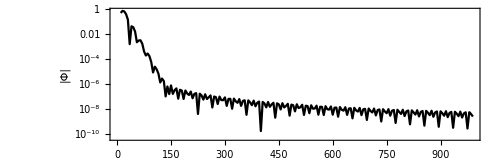

```mathematica
P3=ListLogPlot[Abs[data3],Joined->True,Frame->True,PlotRange->All,PlotStyle->{Black},BaseStyle->{14,FontFamily->"Times"},FrameLabel->{"t","|Φ|"},ImageSize->500,AspectRatio->1/3]
```

# GR WAVE - temporal evolution m=2

## Definitions

```mathematica
m=2;
f[r_]=1-2/r;V[r_,l_]=f[r]((l(l+1))/r^2+f'[r]/r+μ^2-m qB );
fr[rs_]:=Which[TrueQ[rs≥-150],x/.FindRoot[rs==x+2Log[Abs[x/2-1]],{x,2*(1+10^-40),2000},Method->"Secant",WorkingPrecision->64],TrueQ[rs<150],2*(1+10^-40)];frs[r_]=r+2Log[Abs[r/2-1]];
```

## Calculations

Initialization

```mathematica
Do[
v=vmin+j*h;
Y[0,j]=N[Exp[-10^1(v-vc)^2],64];
If[TrueQ[Abs[Y[0,j]]<10^-64],Y[0,j]=0];
Y[j,j]=0;
,{j,0,n}];
Do[
u=umin+i*h;
Do[
v=vmin+j*h;
rrs=(v-u)/2;
rr=fr[rrs];
YS=Y[i-1,j-1];
YE=Y[i-1,j];
YW=Y[i,j-1];
VS=V[rr,vl];
Y[i,j]=(YE+YW)*(16-h^2*VS)/(16+h^2*VS)-YS;
,{j,i+1,n}];
,{i,1,n}]
rs=5;
data4={};
Do[
v=vmin+i*h;
u=v-2*rs;
iu=Round[(u-umin)/h];
iv=Round[(v-vmin)/h];
If[TrueQ[(iu≥0&&iu<n)&&(iv≥0&&iv<n)],t=0.5*(u+v);
data4=Append[data4,{t,Y[iu,iv]}]
];
,{i,0,n}]
```

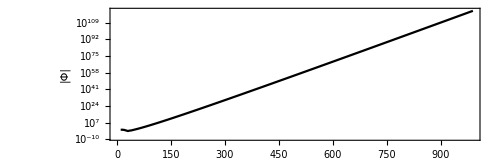

```mathematica
P4=ListLogPlot[Abs[data4],Joined->True,Frame->True,PlotRange->All,PlotStyle->{Black},BaseStyle->{14,FontFamily->"Times"},FrameLabel->{"t","|Φ|"},ImageSize->500,AspectRatio->1/3]
```

# GR WAVE - temporal evolution m=-2

## Definitions

```mathematica
m=-2;
f[r_]=1-2/r;V[r_,l_]=f[r]((l(l+1))/r^2+f'[r]/r+μ^2-m qB );
fr[rs_]:=Which[TrueQ[rs≥-150],x/.FindRoot[rs==x+2Log[Abs[x/2-1]],{x,2*(1+10^-40),2000},Method->"Secant",WorkingPrecision->64],TrueQ[rs<150],2*(1+10^-40)];frs[r_]=r+2Log[Abs[r/2-1]];
```

## Calculations

Initialization

```mathematica
Do[
v=vmin+j*h;
Y[0,j]=N[Exp[-10^1(v-vc)^2],64];
If[TrueQ[Abs[Y[0,j]]<10^-64],Y[0,j]=0];
Y[j,j]=0;
,{j,0,n}];
Do[
u=umin+i*h;
Do[
v=vmin+j*h;
rrs=(v-u)/2;
rr=fr[rrs];
YS=Y[i-1,j-1];
YE=Y[i-1,j];
YW=Y[i,j-1];
VS=V[rr,vl];
Y[i,j]=(YE+YW)*(16-h^2*VS)/(16+h^2*VS)-YS;
,{j,i+1,n}];
,{i,1,n}]
rs=5;
data5={};
Do[
v=vmin+i*h;
u=v-2*rs;
iu=Round[(u-umin)/h];
iv=Round[(v-vmin)/h];
If[TrueQ[(iu≥0&&iu<n)&&(iv≥0&&iv<n)],t=0.5*(u+v);
data5=Append[data5,{t,Y[iu,iv]}]
];
,{i,0,n}]
```

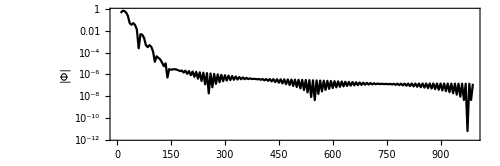

```mathematica
P5=ListLogPlot[Abs[data5],Joined->True,Frame->True,PlotRange->All,PlotStyle->{Black},BaseStyle->{14,FontFamily->"Times"},FrameLabel->{"t","|Φ|"},ImageSize->500,AspectRatio->1/3]
```

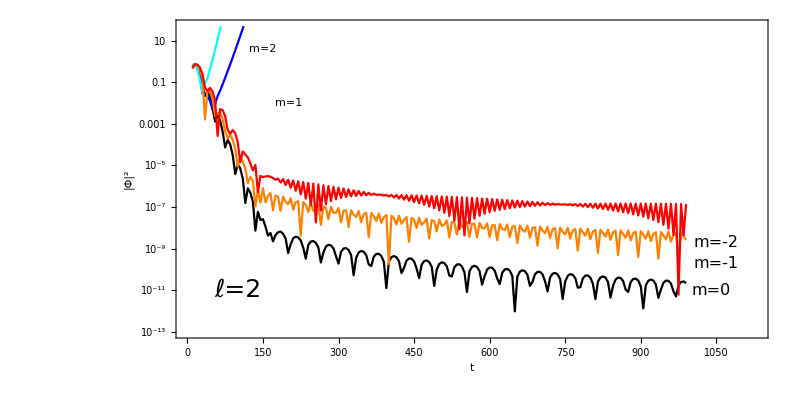

```mathematica
ppp=ListLogPlot[{Abs[data1],Abs[data2],Abs[data4],Abs[data3],Abs[data5]},Joined->True,FrameStyle->Black,Frame->True,PlotRange->{{0,1130},{10^-13,50}},BaseStyle->{20,FontFamily->"Times"},PlotStyle->{Black,Blue,Cyan,Orange,Red},FrameLabel->{"t",TraditionalForm["|Φ|^2"]},Epilog->{Text[Style["m=0",FontSize->16],{1040,Log[10^-11]},Background->White],Text[Style["m=-1",FontSize->16],{1050,Log[2 10^-10]},Background->White],Text[Style["m=-2",FontSize->16],{1050,Log[2 10^-9]}],Text[Style["m=1"],{200,Log[10^-2]}],Text[Style["m=2"],{150,Log[4]}],Text[Style["ℓ=2",FontSize->25],{100,Log[10^-11]},Background->White]},ImageSize->800,AspectRatio->1/2]
```

```mathematica
Export["Bobur/QNM_ScalarField/TeX/PLB/TemporalEvol.pdf",ppp]
```

Bobur/QNM_ScalarField/TeX/PLB/TemporalEvol.pdf

### DATA t=1000

```mathematica
DATA5:={{5.00001,0},{10.00001,-0.45993653719724553},{15.00001,0.7225054946272496},{20.00001,-0.7129549441243237},{25.00001,0.5056408692997238},{30.00001,-0.247194891725185},{35.00001,0.05386219888619617},{40.00001,0.03791160419474064},{45.00001,-0.0534844912926392},{50.00001,0.03538157331904754},{55.00001,-0.013487396388028688},{60.00001,-0.0002599869364931333},{65.00001,0.005115715761295921},{70.00001,-0.004564058359397097},{75.00001,0.00231109822569551},{80.00001,-0.0005127622372645339},{85.00001,-0.00032872558602008183},{90.00001,0.0005026978762230972},{95.00001,-0.00035696411670661505},{100.00001,0.00013155204557748003},{105.00001,0.000014720521382171372},{110.00001,-0.00004718773752901251},{115.00001,0.00003352599471520539},{120.00001,-0.000024501756225240233},{125.00001,0.000012644912563656988},{130.00001,5.806231105076135*^-6},{135.00001,-0.00001057237542649589},{140.00001,5.225586814126671*^-7},{145.00001,3.1616980157448793*^-6},{150.00001,2.7464060517993748*^-6},{155.00001,-2.956757497512976*^-6},{160.00001,-3.0850643456862437*^-6},{165.00001,2.845606144106639*^-6},{170.00001,2.4873262235927234*^-6},{175.00001,-2.0490836451497472*^-6},{180.00001,-2.3340407951915013*^-6},{185.00001,1.5066450109238784*^-6},{190.00001,2.2255373619128165*^-6},{195.00001,-1.156693726793596*^-6},{200.00001,-2.051624710487179*^-6},{205.00001,8.564060186874589*^-7},{210.00001,1.8849627485267655*^-6},{215.00001,-6.078808413401688*^-7},{220.00001,-1.7348976073841964*^-6},{225.00001,4.111868511257351*^-7},{230.00001,1.593274406477559*^-6},{235.00001,-2.5254474644265393*^-7},{240.00001,-1.4607918715205673*^-6},{245.00001,1.2329859027502728*^-7},{250.00001,1.3384629022169314*^-6},{255.00001,-1.8241119428955768*^-8},{260.00001,-1.2256860413405765*^-6},{265.00001,-6.71573168905602*^-8},{270.00001,1.121776367583171*^-6},{275.00001,1.3661343831179741*^-7},{280.00001,-1.0261457350865579*^-6},{285.00001,-1.9300965552950875*^-7},{290.00001,9.38163663922988*^-7},{295.00001,2.386467613262156*^-7},{300.00001,-8.571978129425063*^-7},{305.00001,-2.7539008852806626*^-7},{310.00001,7.826528192562546*^-7},{315.00001,3.047519207798504*^-7},{320.00001,-7.139743608104372*^-7},{325.00001,-3.279640553623083*^-7},{330.00001,6.506501842516237*^-7},{335.00001,3.4603633592071416*^-7},{340.00001,-5.922112733028329*^-7},{345.00001,-3.5980065910651057*^-7},{350.00001,5.382306164431706*^-7},{355.00001,3.699453064725985*^-7},{360.00001,-4.883206822887344*^-7},{365.00001,-3.7704220402708774*^-7},{370.00001,4.421305327945205*^-7},{375.00001,3.8156852392849977*^-7},{380.00001,-3.9934279456613813*^-7},{385.00001,-3.839238792764548*^-7},{390.00001,3.5967062824379847*^-7},{395.00001,3.844441103054591*^-7},{400.00001,-3.2285482015769776*^-7},{405.00001,-3.8341239796855335*^-7},{410.00001,2.886610642298492*^-7},{415.00001,3.8106826091699866*^-7},{420.00001,-2.5687745684794244*^-7},{425.00001,-3.776148737210395*^-7},{430.00001,2.273122117892022*^-7},{435.00001,3.7322504750008946*^-7},{440.00001,-1.9979159245203363*^-7},{445.00001,-3.6804613856136694*^-7},{450.00001,1.741580520735747*^-7},{455.00001,3.6220409122055914*^-7},{460.00001,-1.502685642269851*^-7},{465.00001,-3.558067831266118*^-7},{470.00001,1.2799313025803019*^-7},{475.00001,3.4894680269420724*^-7},{480.00001,-1.0721344747554185*^-7},{485.00001,-3.417037615752972*^-7},{490.00001,8.782171974716929*^-8},{495.00001,3.341462282857143*^-7},{500.00001,-6.97195966692793*^-8},{505.00001,-3.2633335102991616*^-7},{510.00001,5.2817229652133815*^-8},{515.00001,3.183162211363585*^-7},{520.00001,-3.7032429168394416*^-8},{525.00001,-3.101390236160503*^-7},{530.00001,2.2289912608086562*^-8},{535.00001,3.0184001149564275*^-7},{540.00001,-8.52063414261901*^-9},{545.00001,-2.934523313729521*^-7},{550.00001,-4.3388142871909514*^-9},{555.00001,2.85004725214643*^-7},{560.00001,1.6346739606487118*^-8},{565.00001,-2.765221306384329*^-7},{570.00001,-2.7556825233757575*^-8},{575.00001,2.680261913868429*^-7},{580.00001,3.801856083251145*^-8},{585.00001,-2.59535695274069*^-7},{590.00001,-4.777762844191471*^-8},{595.00001,2.510669526827261*^-7},{600.00001,5.6876244818464906*^-8},{605.00001,-2.4263411689989744*^-7},{610.00001,-6.535347452034922*^-8},{615.00001,2.342494647020593*^-7},{620.00001,7.324550864329022*^-8},{625.00001,-2.2592363813017995*^-7},{630.00001,-8.058591390737778*^-8},{635.00001,2.1766584968618101*^-7},{640.00001,8.740586228092111*^-8},{645.00001,-2.094840650033005*^-7},{650.00001,-9.373433431177584*^-8},{655.00001,2.013851592466119*^-7},{660.00001,9.959830307776292*^-8},{665.00001,-1.9337505140304532*^-7},{670.00001,-1.0502290359079269*^-7},{675.00001,1.854588247270609*^-7},{680.00001,1.1003158274445062*^-7},{685.00001,-1.7764082915462963*^-7},{690.00001,-1.1464623653608717*^-7},{695.00001,1.6992477034757133*^-7},{700.00001,1.18887336252334*^-7},{705.00001,-1.6231378977097504*^-7},{710.00001,-1.2277404093454447*^-7},{715.00001,1.5481053335274462*^-7},{720.00001,1.2632430002822098*^-7},{725.00001,-1.4741721090882408*^-7},{730.00001,-1.2955494817164752*^-7},{735.00001,1.4013564953124972*^-7},{740.00001,1.324817907810664*^-7},{745.00001,-1.3296734037623935*^-7},{750.00001,-1.3511968150908373*^-7},{755.00001,1.259134786572024*^-7},{760.00001,1.3748259420224343*^-7},{765.00001,-1.1897499969062945*^-7},{770.00001,-1.3958368825416803*^-7},{775.00001,1.1215261058896893*^-7},{780.00001,1.414353682648866*^-7},{785.00001,-1.0544681813634624*^-7},{790.00001,-1.4304933835274653*^-7},{795.00001,9.885795256865068*^-8},{800.00001,1.4443665299691913*^-7},{805.00001,-9.23861895072913*^-8},{810.00001,-1.4560776297743534*^-7},{815.00001,8.603156893388448*^-8},{820.00001,1.46572557667655*^-7},{825.00001,-7.979401180774183*^-8},{830.00001,-1.4734040422424862*^-7},{835.00001,7.367333527323299*^-8},{840.00001,1.479201827804086*^-7},{845.00001,-6.76692649666244*^-8},{850.00001,-1.4832031996044043*^-7},{855.00001,6.178144649994142*^-8},{860.00001,1.4854881990939124*^-7},{865.00001,-5.600945659542134*^-8},{870.00001,-1.486132912735868*^-7},{875.00001,5.0352811082508226*^-8},{880.00001,1.485209737397714*^-7},{885.00001,-4.481097296022215*^-8},{890.00001,-1.4827876225057766*^-7},{895.00001,3.9383359984468405*^-8},{900.00001,1.478932281394662*^-7},{905.00001,-3.4069349341776214*^-8},{910.00001,-1.4737064141685763*^-7},{915.00001,2.886828484060651*^-8},{920.00001,1.4671698830085828*^-7},{925.00001,-2.377948073999981*^-8},{930.00001,-1.459379891710361*^-7},{935.00001,1.8802225848781178*^-8},{940.00001,1.4503911511656322*^-7},{945.00001,-1.3935787298144819*^-8},{950.00001,-1.4402560312521792*^-7},{955.00001,9.17941370487842*^-9},{960.00001,1.4290247057852642*^-7},{965.00001,-4.532338926890882*^-9},{970.00001,-1.4167452688281477*^-7},{975.00001,-6.217269372861897*^-12},{980.00001,1.4034638742594887*^-7},{985.00001,4.437045737829046*^-9},{990.00001,-1.3892248444904323*^-7}}
DATA4:={{5.00001,0},{10.00001,-0.6730885037464347},{15.00001,0.7288176704833594},{20.00001,-0.4293497652567597},{25.00001,0.12004296882489757},{30.00001,-0.031485042629230534},{35.00001,-0.09061376082136835},{40.00001,-0.1524315874936195},{45.00001,-0.44783539638421144},{50.00001,-1.2512728835428104},{55.00001,-3.690573029294672},{60.00001,-11.335814555403521},{65.00001,-36.003427529041204},{70.00001,-117.74386592008796},{75.00001,-394.97784958800094},{80.00001,-1354.861489074599},{85.00001,-4740.008953859937},{90.00001,-16876.412508269357},{95.00001,-61037.60442674776},{100.00001,-223897.06259297323},{105.00001,-831852.1802413906},{110.00001,-3.1266787998415576*^6},{115.00001,-1.1877308652662799*^7},{120.00001,-4.555791951550489*^7},{125.00001,-1.7631148880156657*^8},{130.00001,-6.879667058104364*^8},{135.00001,-2.704936566787103*^9},{140.00001,-1.0710535850378582*^10},{145.00001,-4.2689022936746826*^10},{150.00001,-1.7119068454567752*^11},{155.00001,-6.904459726406738*^11},{160.00001,-2.7996781239042715*^12},{165.00001,-1.1409665848162412*^13},{170.00001,-4.671909959174701*^13},{175.00001,-1.9215614028492384*^14},{180.00001,-7.936771386416862*^14},{185.00001,-3.291271550061006*^15},{190.00001,-1.3700051415431564*^16},{195.00001,-5.723146247700298*^16},{200.00001,-2.398963268610125*^17},{205.00001,-1.0088258075978358*^18},{210.00001,-4.255450549294903*^18},{215.00001,-1.800318620596333*^19},{220.00001,-7.637823885413*^19},{225.00001,-3.2490189266096226*^20},{230.00001,-1.3856279604347624*^21},{235.00001,-5.923870475180126*^21},{240.00001,-2.5385440156232653*^22},{245.00001,-1.0902912311390317*^23},{250.00001,-4.692885794068715*^23},{255.00001,-2.0241392327368705*^24},{260.00001,-8.748007272904077*^24},{265.00001,-3.7880320353807493*^25},{270.00001,-1.6433237520802044*^26},{275.00001,-7.141813791112965*^26},{280.00001,-3.109154500719956*^27},{285.00001,-1.3558087255843147*^28},{290.00001,-5.921778952280265*^28},{295.00001,-2.590479603161277*^29},{300.00001,-1.1349066221736069*^30},{305.00001,-4.9793299202118786*^30},{310.00001,-2.187723217462149*^31},{315.00001,-9.625103184620005*^31},{320.00001,-4.2402523580020435*^32},{325.00001,-1.8703974448660957*^33},{330.00001,-8.26067186266338*^33},{335.00001,-3.652752540219248*^34},{340.00001,-1.6170869770257738*^35},{345.00001,-7.167047042881496*^35},{350.00001,-3.1799991275601634*^36},{355.00001,-1.4124735622870248*^37},{360.00001,-6.280402846578359*^37},{365.00001,-2.795350775848067*^38},{370.00001,-1.2454177424868413*^39},{375.00001,-5.554084243497583*^39},{380.00001,-2.4792353515188026*^40},{385.00001,-1.1076959011175138*^41},{390.00001,-4.953485102972956*^41},{395.00001,-2.2170684040814606*^42},{400.00001,-9.93152642236467*^42},{405.00001,-4.4525898410644417*^43},{410.00001,-1.9978394535194755*^44},{415.00001,-8.971218225144937*^44},{420.00001,-4.031598070024052*^45},{425.00001,-1.8131357431636129*^46},{430.00001,-8.16024639561666*^46},{435.00001,-3.675267222614442*^47},{440.00001,-1.6564576785696087*^48},{445.00001,-7.470864362824515*^48},{450.00001,-3.371739204235225*^49},{455.00001,-1.5227319537934643*^50},{460.00001,-6.881343806694189*^50},{465.00001,-3.1116984547939815*^51},{470.00001,-1.4079606991448605*^52},{475.00001,-6.374510603685815*^52},{480.00001,-2.8877602111128904*^53},{485.00001,-1.3089655431518251*^54},{490.00001,-5.9366726823798524*^54},{495.00001,-2.694020822272266*^55},{500.00001,-1.2231987755484862*^56},{505.00001,-5.55682609976494*^56},{510.00001,-2.525723576321382*^57},{515.00001,-1.1486025302832326*^58},{520.00001,-5.226060997854455*^58},{525.00001,-2.379007829104824*^59},{530.00001,-1.083502727649881*^60},{535.00001,-4.937112770562368*^60},{540.00001,-2.2507188669313475*^61},{545.00001,-1.0265284471459364*^62},{550.00001,-4.684019834031492*^62},{555.00001,-2.138262505377802*^63},{560.00001,-9.765500939694665*^63},{565.00001,-4.4618604319349684*^64},{570.00001,-2.0394929597830689*^65},{575.00001,-9.326315861893793*^65},{580.00001,-4.266548582361568*^66},{585.00001,-1.9526256869151597*^67},{590.00001,-8.939930954748966*^67},{595.00001,-4.09467466892557*^68},{600.00001,-1.8761691296277626*^69},{605.00001,-8.599817988360987*^69},{610.00001,-3.943380012298899*^70},{615.00001,-1.8088708875849395*^71},{620.00001,-8.300487600517965*^71},{625.00001,-3.8102575088816715*^72},{630.00001,-1.7496749824626604*^73},{635.00001,-8.037305368682363*^73},{640.00001,-3.6932724152923283*^74},{645.00001,-1.6976877179934091*^75},{650.00001,-7.80634457860297*^75},{655.00001,-3.590698812785774*^76},{660.00001,-1.6521502448216503*^77},{665.00001,-7.604267684109586*^77},{670.00001,-3.5010683580784045*^78},{675.00001,-1.6124163905134926*^79},{680.00001,-7.428230345789581*^79},{685.00001,-3.4231287235184863*^80},{690.00001,-1.57793465042328*^81},{695.00001,-7.275803349490635*^81},{700.00001,-3.3558097255852326*^82},{705.00001,-1.5482334867075404*^83},{710.00001,-7.144908768374497*^83},{715.00001,-3.298195589999339*^84},{720.00001,-1.522909272867496*^85},{725.00001,-7.033767537094171*^85},{730.00001,-3.2495021427551594*^86},{735.00001,-1.5016163658063227*^87},{740.00001,-6.9408562202748135*^87},{745.00001,-3.209057976944516*^88},{750.00001,-1.4840588981078047*^89},{755.00001,-6.864871228291657*^89},{760.00001,-3.17628884558068*^90},{765.00001,-1.4699839685476739*^91},{770.00001,-6.804699096807895*^91},{775.00001,-3.150704685601127*^92},{780.00001,-1.459175974965035*^93},{785.00001,-6.759391728791464*^93},{790.00001,-3.1318887988011098*^94},{795.00001,-1.4514518851594485*^95},{800.00001,-6.72814571816048*^95},{805.00001,-3.119488809786097*^96},{810.00001,-1.4466572818756634*^97},{815.00001,-6.710285047294157*^97},{820.00001,-3.1132090952374706*^98},{825.00001,-1.4446630497702113*^99},{830.00001,-6.705246587274345*^99},{835.00001,-3.1128044374616203*^100},{840.00001,-1.4453625974668326*^101},{845.00001,-6.712567938121018*^101},{850.00001,-3.1180747018223275*^102},{855.00001,-1.4486695278773824*^103},{860.00001,-6.731877232712735*^103},{865.00001,-3.128860374895211*^104},{870.00001,-1.4545156860183438*^105},{875.00001,-6.762884597325388*^105},{880.00001,-3.145038830064479*^106},{885.00001,-1.4628495264552681*^107},{890.00001,-6.805375017459903*^107},{895.00001,-3.166521211373294*^108},{900.00001,-1.4736347529254143*^109},{905.00001,-6.859202402705102*^109},{910.00001,-3.1932498459517646*^110},{915.00001,-1.4868491911402427*^111},{920.00001,-6.924284681004601*^111},{925.00001,-3.2251961112248574*^112},{930.00001,-1.5024838626570498*^113},{935.00001,-7.000599782589994*^113},{940.00001,-3.2623586960833047*^114},{945.00001,-1.520542233348826*^115},{950.00001,-7.088182398358398*^115},{955.00001,-3.3047622058631955*^116},{960.00001,-1.5410396146414332*^117},{965.00001,-7.187121417675268*^117},{970.00001,-3.352456069781374*^118},{975.00001,-1.56400269952358*^119},{980.00001,-7.297557967315754*^119},{985.00001,-3.405513716775665*^120},{990.00001,-1.5894692185236758*^121}}
DATA3:={{5.00001,0},{10.00001,-0.5079653440770465},{15.00001,0.7504694643883278},{20.00001,-0.6663072811389237},{25.00001,0.4017426793596922},{30.00001,-0.14772224677056633},{35.00001,0.0016227695606757797},{40.00001,0.04356421014486325},{45.00001,-0.03631610536143887},{50.00001,0.016466406904088324},{55.00001,-0.002312693777365914},{60.00001,-0.003163483723541978},{65.00001,0.003305171196539601},{70.00001,-0.001756677114267336},{75.00001,0.0004212207049687578},{80.00001,0.00020055370611200027},{85.00001,-0.0002880599260897427},{90.00001,0.00017652745874265392},{95.00001,-0.00005990963066520516},{100.00001,-8.78412827593137*^-6},{105.00001,0.000025558695825458723},{110.00001,-0.000015779406365857636},{115.00001,7.066274802618754*^-6},{120.00001,-1.395778968589513*^-6},{125.00001,-2.862959421899137*^-6},{130.00001,1.7786103681188226*^-6},{135.00001,1.062788482787438*^-7},{140.00001,6.663589297007186*^-7},{145.00001,-1.6363061971228558*^-7},{150.00001,-8.095535404016878*^-7},{155.00001,-1.702373844045252*^-7},{160.00001,3.3591367101553*^-7},{165.00001,4.6707257542254904*^-7},{170.00001,7.046954332129374*^-8},{175.00001,-3.639409131243068*^-7},{180.00001,-3.122365388846741*^-7},{185.00001,6.657191729388439*^-8},{190.00001,3.175126365325673*^-7},{195.00001,1.826271581829632*^-7},{200.00001,-1.3857563267140858*^-7},{205.00001,-2.61042845328959*^-7},{210.00001,-7.557798130816586*^-8},{215.00001,1.7096368646907612*^-7},{220.00001,1.9468299247680538*^-7},{225.00001,-4.20408310855009*^-9},{230.00001,-1.7483600281714692*^-7},{235.00001,-1.2762464737299715*^-7},{240.00001,5.926156935554153*^-8},{245.00001,1.5817188495015825*^-7},{250.00001,6.602136836451347*^-8},{255.00001,-9.193616564620113*^-8},{260.00001,-1.2841759973927305*^-7},{265.00001,-1.3915321917362995*^-8},{270.00001,1.0534696291274946*^-7},{275.00001,9.189049679156556*^-8},{280.00001,-2.6246129339940342*^-8},{285.00001,-1.0319716358698505*^-7},{290.00001,-5.38670312743888*^-8},{295.00001,5.3481863603704854*^-8},{300.00001,8.950548154287869*^-8},{305.00001,1.8536242435349993*^-8},{310.00001,-6.806617395204073*^-8},{315.00001,-6.834927998770928*^-8},{320.00001,1.104839347790116*^-8},{325.00001,7.12965168691647*^-8},{330.00001,4.3600687780959875*^-8},{335.00001,-3.29743861221896*^-8},{340.00001,-6.523252387550567*^-8},{345.00001,-1.8687346784825814*^-8},{350.00001,4.641988815625413*^-8},{355.00001,5.241429171843043*^-8},{360.00001,-3.6011237089203108*^-9},{365.00001,-5.1541923550620495*^-8},{370.00001,-3.5576984903003935*^-8},{375.00001,2.1244932140388353*^-8},{380.00001,4.930813531454472*^-8},{385.00001,1.738147431863665*^-8},{390.00001,-3.3054461956364986*^-8},{395.00001,-4.1284787685278345*^-8},{400.00001,-1.8067682958365434*^-10},{405.00001,3.865674939893875*^-8},{410.00001,2.9399138909106964*^-8},{415.00001,-1.416154709674624*^-8},{420.00001,-3.841300563690361*^-8},{425.00001,-1.5697177592498327*^-8},{430.00001,2.4386996938628242*^-8},{435.00001,3.327868872324061*^-8},{440.00001,2.118036177260753*^-9},{445.00001,-2.9889556110460735*^-8},{450.00001,-2.462287787060989*^-8},{455.00001,9.695719407899472*^-9},{460.00001,3.0692612195544714*^-8},{465.00001,1.4027009714094319*^-8},{470.00001,-1.853688144479961*^-8},{475.00001,-2.736526731412201*^-8},{480.00001,-3.0841672558562113*^-9},{485.00001,2.3712137725345065*^-8},{490.00001,2.0890775995398447*^-8},{495.00001,-6.781051632870397*^-9},{500.00001,-2.5057538175073372*^-8},{505.00001,-1.2504713261274836*^-8},{510.00001,1.4455291649084381*^-8},{515.00001,2.2894696886516994*^-8},{520.00001,3.5224380313668947*^-9},{525.00001,-1.9229943877759632*^-8},{530.00001,-1.793748149242842*^-8},{535.00001,4.824693336453451*^-9},{540.00001,2.0839490535309397*^-8},{545.00001,1.1163600829487085*^-8},{550.00001,-1.1527126354556036*^-8},{555.00001,-1.9445141093474263*^-8},{560.00001,-3.6683547288409217*^-9},{565.00001,1.5895674364991428*^-8},{570.00001,1.5570206278527726*^-8},{575.00001,-3.4813713438366325*^-9},{580.00001,-1.7612881427598394*^-8},{585.00001,-9.998628741061532*^-9},{590.00001,9.376044022664408*^-9},{595.00001,1.673510074468654*^-8},{600.00001,3.6515149279934937*^-9},{605.00001,-1.3361628765638567*^-8},{610.00001,-1.3649031915383202*^-8},{615.00001,2.5419561700029666*^-9},{620.00001,1.5097738432693192*^-8},{625.00001,8.991519567179539*^-9},{630.00001,-7.763312000516766*^-9},{635.00001,-1.4571914787036221*^-8},{640.00001,-3.545188282156662*^-9},{645.00001,1.1399627482235888*^-8},{650.00001,1.2071677692007879*^-8},{655.00001,-1.8754644226675474*^-9},{660.00001,-1.3104582415622217*^-8},{665.00001,-8.120977981740198*^-9},{670.00001,6.532692368914374*^-9},{675.00001,1.2820667442549164*^-8},{680.00001,3.391608432552703*^-9},{685.00001,-9.855639904493374*^-9},{690.00001,-1.0762580332417586*^-8},{695.00001,1.3974525796732305*^-9},{700.00001,1.1501937358176963*^-8},{705.00001,7.36669043038733*^-9},{710.00001,-5.579116632554129*^-9},{715.00001,-1.1384906649021232*^-8},{720.00001,-3.2154046182230545*^-9},{725.00001,8.62308154189894*^-9},{730.00001,9.665249868916104*^-9},{735.00001,-1.052093138526612*^-9},{740.00001,-1.0196536962015403*^-8},{745.00001,-6.710695085447448*^-9},{750.00001,4.8302175572498095*^-9},{755.00001,1.019437790995538*^-8},{760.00001,3.0309834729192057*^-9},{765.00001,-7.626565364834087*^-9},{770.00001,-8.736943367706349*^-9},{775.00001,8.016537468568518*^-10},{780.00001,9.120904884789891*^-9},{785.00001,6.137651399392884*^-9},{790.00001,-4.235083090023849*^-9},{795.00001,-9.19703702781878*^-9},{800.00001,-2.8467050894133662*^-9},{805.00001,6.811719472958947*^-9},{810.00001,7.944936646445012*^-9},{815.00001,-6.201308400718312*^-10},{820.00001,-8.22535420849217*^-9},{825.00001,-5.634674530684099*^-9},{830.00001,3.757210752479548*^-9},{835.00001,8.353734706779618*^-9},{840.00001,2.6673046047831267*^-9},{845.00001,-6.138637410283984*^-9},{850.00001,-7.26389094874801*^-9},{855.00001,4.892905238572316*^-10},{860.00001,7.47271116127781*^-9},{865.00001,5.191025083420592*^-9},{870.00001,-3.3699817302162176*^-9},{875.00001,-7.634607236727923*^-9},{880.00001,-2.4953252834931986*^-9},{885.00001,5.5775628759207046*^-9},{890.00001,6.673977031114895*^-9},{895.00001,-3.9614888655946667*^-10},{900.00001,-6.834760890761349*^-9},{905.00001,-4.797773683219413*^-9},{910.00001,3.053682663973881*^-9},{915.00001,7.016582971510959*^-9},{920.00001,2.3319821099237932*^-9},{925.00001,-5.105989629386372*^-9},{930.00001,-6.159519341185347*^-9},{935.00001,3.3133101870073245*^-10},{940.00001,6.289805762899202*^-9},{945.00001,4.447494870209074*^-9},{950.00001,-2.7935102435218174*^-9},{955.00001,-6.4816273692859005*^-9},{960.00001,-2.1776891348907924*^-9},{965.00001,4.70667166658139*^-9},{970.00001,5.708009320243821*^-9},{975.00001,-2.879837075454055*^-10},{980.00001,-5.820958708569594*^-9},{985.00001,-4.1340014670035566*^-9},{990.00001,2.578205622859537*^-9}}
DATA2:={{5.00001,0},{10.00001,-0.6141709244296405},{15.00001,0.7595970183284315},{20.00001,-0.5129883827920185},{25.00001,0.20626101877348707},{30.00001,-0.02862383860831144},{35.00001,-0.028352429523716992},{40.00001,0.022265357205680604},{45.00001,-0.01280726801481613},{50.00001,-0.0047788060312773505},{55.00001,-0.008977601947739172},{60.00001,-0.021530361594633535},{65.00001,-0.03946398506532216},{70.00001,-0.08041131968130702},{75.00001,-0.1652213848863604},{80.00001,-0.3451742254542939},{85.00001,-0.7332758889235204},{90.00001,-1.57951925225451},{95.00001,-3.4460476661636816},{100.00001,-7.605379185037761},{105.00001,-16.961534967170635},{110.00001,-38.190680746702704},{115.00001,-86.74574564347043},{120.00001,-198.62308808506017},{125.00001,-458.1730020373735},{130.00001,-1064.15554455573},{135.00001,-2487.3688592748686},{140.00001,-5848.45032950983},{145.00001,-13827.145318204031},{150.00001,-32859.27285754653},{155.00001,-78464.74467514525},{160.00001,-188214.45657497458},{165.00001,-453393.5623010086},{170.00001,-1.0965642550735539*^6},{175.00001,-2.662138774107632*^6},{180.00001,-6.485967752472497*^6},{185.00001,-1.5855620329654891*^7},{190.00001,-3.888476004669571*^7},{195.00001,-9.565167128631708*^7},{200.00001,-2.3597019349488607*^8},{205.00001,-5.837305698520449*^8},{210.00001,-1.447778098801045*^9},{215.00001,-3.5997582354543595*^9},{220.00001,-8.971756725193016*^9},{225.00001,-2.2411389116319057*^10},{230.00001,-5.610537574950107*^10},{235.00001,-1.4074876291550757*^11},{240.00001,-3.537949292458435*^11},{245.00001,-8.910258738466875*^11},{250.00001,-2.2481620732617974*^12},{255.00001,-5.682407181811557*^12},{260.00001,-1.4387162666385533*^13},{265.00001,-3.6486174057068945*^13},{270.00001,-9.26756631438855*^13},{275.00001,-2.3575588763793512*^14},{280.00001,-6.006139969100762*^14},{285.00001,-1.532294445110483*^15},{290.00001,-3.914550044246985*^15},{295.00001,-1.0013694849518292*^16},{300.00001,-2.5648429188599204*^16},{305.00001,-6.577533609828885*^16},{310.00001,-1.6888228803269555*^17},{315.00001,-4.341177216546451*^17},{320.00001,-1.1171660584657059*^18},{325.00001,-2.8780603722420823*^18},{330.00001,-7.422322749447916*^18},{335.00001,-1.916125683631964*^19},{340.00001,-4.951530085410911*^19},{345.00001,-1.2807776468343305*^20},{350.00001,-3.316004327944162*^20},{355.00001,-8.59314452807114*^20},{360.00001,-2.2288145843248643*^21},{365.00001,-5.785889414169411*^21},{370.00001,-1.5032481171873404*^22},{375.00001,-3.9088225014090845*^22},{380.00001,-1.0172009110535894*^23},{385.00001,-2.6491354777880694*^23},{390.00001,-6.904459773891517*^23},{395.00001,-1.8008400378628494*^24},{400.00001,-4.700375685435728*^24},{405.00001,-1.2277060504741564*^25},{410.00001,-3.2088785755632688*^25},{415.00001,-8.392709067514341*^25},{420.00001,-2.19651532766404*^26},{425.00001,-5.752318436862439*^26},{430.00001,-1.5073769479161578*^27},{435.00001,-3.952437051279529*^27},{440.00001,-1.0369702099710305*^28},{445.00001,-2.7222004821728183*^28},{450.00001,-7.150244843173848*^28},{455.00001,-1.879158250218347*^29},{460.00001,-4.941311806150971*^29},{465.00001,-1.300027746818896*^30},{470.00001,-3.422075565851169*^30},{475.00001,-9.012566604765169*^30},{480.00001,-2.374787478386062*^31},{485.00001,-6.260571469519822*^31},{490.00001,-1.6512464506907244*^32},{495.00001,-4.3572689287754256*^32},{500.00001,-1.1503165355364388*^33},{505.00001,-3.0382044060163724*^33},{510.00001,-8.02803872404588*^33},{515.00001,-2.122223381080791*^34},{520.00001,-5.612525504419928*^34},{525.00001,-1.484935833654305*^35},{530.00001,-3.930391427086914*^35},{535.00001,-1.0407331772408597*^36},{540.00001,-2.756863657151023*^36},{545.00001,-7.305675382563639*^36},{550.00001,-1.9367413858203884*^37},{555.00001,-5.136249835992654*^37},{560.00001,-1.3626396997159865*^38},{565.00001,-3.616375720392384*^38},{570.00001,-9.601099145399302*^38},{575.00001,-2.5498852077605772*^39},{580.00001,-6.774386969087272*^39},{585.00001,-1.8003898878028417*^40},{590.00001,-4.786387782656373*^40},{595.00001,-1.272892040126575*^41},{600.00001,-3.3862211124717345*^41},{605.00001,-9.011080008526402*^41},{610.00001,-2.3986890967137143*^42},{615.00001,-6.387111606103104*^42},{620.00001,-1.7012430937581747*^43},{625.00001,-4.532705675373917*^43},{630.00001,-1.20802503566764*^44},{635.00001,-3.2204730133182485*^44},{640.00001,-8.587896400552349*^44},{645.00001,-2.290738238785554*^45},{650.00001,-6.112007048541482*^45},{655.00001,-1.6312110582443037*^46},{660.00001,-4.354643982126474*^46},{665.00001,-1.1628123514094025*^47},{670.00001,-3.1058425541065366*^47},{675.00001,-8.297751518072109*^47},{680.00001,-2.2174355771857823*^48},{685.00001,-5.927200723893009*^48},{690.00001,-1.5847281459403689*^49},{695.00001,-4.2380388019864306*^49},{700.00001,-1.1336490959794862*^50},{705.00001,-3.033154229572516*^50},{710.00001,-8.117290193280117*^50},{715.00001,-2.1728363129444333*^51},{720.00001,-5.8175612805747454*^51},{725.00001,-1.5579432199797352*^52},{730.00001,-4.1730895002043226*^52},{735.00001,-1.1180415032208819*^53},{740.00001,-2.9960638733688793*^53},{745.00001,-8.030376630134732*^53},{750.00001,-2.152837636138455*^54},{755.00001,-5.772660166107375*^54},{760.00001,-1.5482066039384748*^55},{765.00001,-4.1530669268578897*^55},{770.00001,-1.1142815410053602*^56},{775.00001,-2.9902386973551147*^56},{780.00001,-8.026027388615556*^56},{785.00001,-2.1546574701889908*^57},{790.00001,-5.7854566846792784*^57},{795.00001,-1.5537382608089115*^58},{800.00001,-4.1734758212511813*^58},{805.00001,-1.1212354211614083*^59},{810.00001,-3.012823142924024*^59},{815.00001,-8.097061980729318*^59},{820.00001,-2.176493498702974*^60},{825.00001,-5.85143623579677*^60},{830.00001,-1.5734099557142476*^61},{835.00001,-4.2315040739246865*^61},{840.00001,-1.1382043434137744*^62},{845.00001,-3.062086731232458*^62},{850.00001,-8.239212292012552*^62},{855.00001,-2.2172979309507843*^63},{860.00001,-5.9680406732843644*^63},{865.00001,-1.6066011918480262*^64},{870.00001,-4.3256584077580147*^64},{875.00001,-1.1648323737397401*^65},{880.00001,-3.137191159421994*^65},{885.00001,-8.450533865710853*^65},{890.00001,-2.276628727902146*^66},{895.00001,-6.134292453979251*^66},{900.00001,-1.653104292865169*^67},{905.00001,-4.455524775997456*^67},{910.00001,-1.201045991713559*^68},{915.00001,-3.2380378647543213*^68},{920.00001,-8.731021782257652*^68},{925.00001,-2.354552882712313*^69},{930.00001,-6.350551316591237*^69},{935.00001,-1.7130632506825273*^70},{940.00001,-4.621614846941307*^70},{945.00001,-1.2470156019173047*^71},{950.00001,-3.36517166895863*^71},{955.00001,-9.082369834680028*^71},{960.00001,-2.4515863443775643*^72},{965.00001,-6.618364737326708*^72},{970.00001,-1.7869365919455106*^73},{975.00001,-4.825274057708232*^73},{980.00001,-1.3031328412994268*^74},{985.00001,-3.5197249834446573*^74},{990.00001,-9.50783394939316*^74}}
DATA1:={{5.00001,0},{10.00001,-0.5592617388344382},{15.00001,0.7645465466651282},{20.00001,-0.5974613692053264},{25.00001,0.29803040803445663},{30.00001,-0.07464319608542644},{35.00001,-0.021840453995395886},{40.00001,0.03561031817300854},{45.00001,-0.020408969278237956},{50.00001,0.0055901514339002},{55.00001,0.0012939809609847155},{60.00001,-0.0024339364893076992},{65.00001,0.0014491930115411958},{70.00001,-0.00042199502537719133},{75.00001,-0.00007361256519996975},{80.00001,0.00016581400650895318},{85.00001,-0.0001027965020023559},{90.00001,0.00003156651699588751},{95.00001,3.896041180762804*^-6},{100.00001,-0.000011281926192514308},{105.00001,7.279564364629044*^-6},{110.00001,-2.328288982182059*^-6},{115.00001,-1.5590523642607113*^-7},{120.00001,7.931453404600915*^-7},{125.00001,-4.917863515925923*^-7},{130.00001,1.8507499140752693*^-7},{135.00001,7.342929072229036*^-9},{140.00001,-5.914069950340437*^-8},{145.00001,2.39469638252131*^-8},{150.00001,-2.6202325143468184*^-8},{155.00001,-1.1586440520791818*^-8},{160.00001,-4.273472844470738*^-9},{165.00001,-5.641120120497163*^-9},{170.00001,2.2481896282124156*^-9},{175.00001,4.60195444957347*^-9},{180.00001,6.163657633039985*^-9},{185.00001,6.693752831734319*^-9},{190.00001,5.174045847344378*^-9},{195.00001,3.0764272412763475*^-9},{200.00001,6.145705185593332*^-10},{205.00001,-1.6255289053330902*^-9},{210.00001,-3.1358256888286055*^-9},{215.00001,-3.766546371138981*^-9},{220.00001,-3.4908082589338374*^-9},{225.00001,-2.4995927514702748*^-9},{230.00001,-1.1096259954711655*^-9},{235.00001,3.313547386663842*^-10},{240.00001,1.5061046164511856*^-9},{245.00001,2.1977027433382517*^-9},{250.00001,2.320195567405143*^-9},{255.00001,1.9192722866568054*^-9},{260.00001,1.1472441908170296*^-9},{265.00001,2.1719625629226084*^-10},{270.00001,-6.494472196772714*^-10},{275.00001,-1.271062137987209*^-9},{280.00001,-1.5401234742606777*^-9},{285.00001,-1.4377939687589333*^-9},{290.00001,-1.0280667122482171*^-9},{295.00001,-4.3485950923594627*^-10},{300.00001,1.912656723687466*^-10},{305.00001,7.085691933384008*^-10},{310.00001,1.0140098821280865*^-9},{315.00001,1.0617029960773051*^-9},{320.00001,8.67141372130589*^-10},{325.00001,4.976866803851101*^-10},{330.00001,5.271203439945259*^-11},{335.00001,-3.6131647155774063*^-10},{340.00001,-6.549349728282531*^-10},{345.00001,-7.738038434859028*^-10},{350.00001,-7.074542497017718*^-10},{355.00001,-4.876020384780543*^-10},{360.00001,-1.7733161644099289*^-10},{365.00001,1.456794074021898*^-10},{370.00001,4.0769307291944225*^-10},{375.00001,5.549774401629672*^-10},{380.00001,5.640761233276406*^-10},{385.00001,4.4450166526805195*^-10},{390.00001,2.338788592759522*^-10},{395.00001,-1.276795853232709*^-11},{400.00001,-2.3674217781571316*^-10},{405.00001,-3.8912888566984923*^-10},{410.00001,-4.4100466564315337*^-10},{415.00001,-3.8838663315343363*^-10},{420.00001,-2.5121311951358605*^-10},{425.00001,-6.70406897910739*^-11},{430.00001,1.1874074603357379*^-10},{435.00001,2.637330872450248*^-10},{440.00001,3.3788666283892364*^-10},{445.00001,3.294028473767708*^-10},{450.00001,2.461009705972821*^-10},{455.00001,1.1226070835723351*^-10},{460.00001,-3.803038963907715*^-11},{465.00001,-1.6928981807855375*^-10},{470.00001,-2.52791958785831*^-10},{475.00001,-2.7264059194684546*^-10},{480.00001,-2.2852849485706081*^-10},{485.00001,-1.347755299162636*^-10},{490.00001,-1.611206364873461*^-11},{495.00001,9.863267171570972*^-11},{500.00001,1.8336942618207502*^-10},{505.00001,2.205306708826555*^-10},{510.00001,2.0454973277931563*^-10},{515.00001,1.4238790639453403*^-10},{520.00001,5.117300990211396*^-11},{525.00001,-4.633911346984688*^-11},{530.00001,-1.2731568678208157*^-10},{535.00001,-1.7408266149128778*^-10},{540.00001,-1.7787347320446986*^-10},{545.00001,-1.4031919087958354*^-10},{550.00001,-7.247108661178762*^-11},{555.00001,8.276880075794629*^-12},{560.00001,8.254703828928233*^-11},{565.00001,1.3354408243719776*^-10},{570.00001,1.5077539646661848*^-10},{575.00001,1.3211678099003346*^-10},{580.00001,8.38442909247788*^-11},{585.00001,1.8731273877267136*^-11},{590.00001,-4.7245203665475445*^-11},{595.00001,-9.875872865075302*^-11},{600.00001,-1.2463640765748223*^-10},{605.00001,-1.2021932038916841*^-10},{610.00001,-8.810002538951306*^-11},{615.00001,-3.715030382416127*^-11},{620.00001,1.984940551736147*^-11},{625.00001,6.936389184223629*^-11},{630.00001,1.0027087841562487*^-10},{635.00001,1.0631477275303851*^-10},{640.00001,8.73154959094657*^-11},{645.00001,4.891068084326601*^-11},{650.00001,9.692348186881703*^-13},{655.00001,-4.49008614716852*^-11},{660.00001,-7.812766337401569*^-11},{665.00001,-9.157546041046363*^-11},{670.00001,-8.304160013341215*^-11},{675.00001,-5.553593890302664*^-11},{680.00001,-1.6340506989765314*^-11},{685.00001,2.4877055201572808*^-11},{690.00001,5.841880836387511*^-11},{695.00001,7.681160598495117*^-11},{700.00001,7.644498714644209*^-11},{705.00001,5.823724056415007*^-11},{710.00001,2.7223327198485205*^-11},{715.00001,-8.798268311207515*^-12},{720.00001,-4.1202112284047866*^-11},{725.00001,-6.257767485240318*^-11},{730.00001,-6.840492905675243*^-11},{735.00001,-5.798351734738362*^-11},{740.00001,-3.443398659148284*^-11},{745.00001,-3.810326938634423*^-12},{750.00001,2.643402404912497*^-11},{755.00001,4.9242830028248613*^-11},{760.00001,5.958637779737668*^-11},{765.00001,5.555251616219471*^-11},{770.00001,3.866682318892411*^-11},{775.00001,1.3397152644341583*^-11},{780.00001,-1.4006156701038367*^-11},{785.00001,-3.704267297388227*^-11},{790.00001,-5.0489078018814775*^-11},{795.00001,-5.157046927695734*^-11},{800.00001,-4.051394702415968*^-11},{805.00001,-2.0378239257410344*^-11},{810.00001,3.768895369576002*^-12},{815.00001,2.6114086645588093*^-11},{820.00001,4.1486122269337337*^-11},{825.00001,4.65415441282488*^-11},{830.00001,4.0480251215984647*^-11},{835.00001,2.5136135717210842*^-11},{840.00001,4.452068214350226*^-12},{845.00001,-1.652153641466096*^-11},{850.00001,-3.285135156613993*^-11},{855.00001,-4.0870914610226707*^-11},{860.00001,-3.8995818272998926*^-11},{865.00001,-2.8019967508759863*^-11},{870.00001,-1.0844693776381951*^-11},{875.00001,8.276019608202865*^-12},{880.00001,2.478092958118947*^-11},{885.00001,3.488202026588425*^-11},{890.00001,3.642659907854548*^-11},{895.00001,2.934666681372071*^-11},{900.00001,1.5601788566152217*^-11},{905.00001,-1.3487601984298275*^-12},{910.00001,-1.740904072264407*^-11},{915.00001,-2.8831338230081737*^-11},{920.00001,-3.308289543715216*^-11},{925.00001,-2.940154818673323*^-11},{930.00001,-1.891618724355648*^-11},{935.00001,-4.318162831055243*^-12},{940.00001,1.08211656565684*^-11},{945.00001,2.291930944960429*^-11},{950.00001,2.9225783795999924*^-11},{955.00001,2.8441030208608263*^-11},{960.00001,2.097636968537676*^-11},{965.00001,8.802673249703244*^-12},{970.00001,-5.062836769987903*^-12},{975.00001,-1.729958883010914*^-11},{980.00001,-2.5074229356636303*^-11},{985.00001,-2.669273544306584*^-11},{990.00001,-2.1963995675227356*^-11}}
```

### DATA t=150

```mathematica
D5:={{5.00001,0},{5.50001,-0.018795164970388002},{6.00001,-0.03369067982026446},{6.50001,-0.04420033204768949},{7.00001,-0.05010006853577854},{7.50001,-0.05143740016324288},{8.00001,-0.04852370055970382},{8.50001,-0.041909568859551764},{9.00001,-0.032380517408202115},{9.50001,-0.08500301449746495},{10.00001,-0.7521626344343847},{10.50001,0.367463012474859},{11.00001,0.36445456587222},{11.50001,0.26492066087126376},{12.00001,0.17736062577550887},{12.50001,0.10304004720516646},{13.00001,0.04251751840598067},{13.50001,-0.004271278458298569},{14.00001,-0.03795609516214548},{14.50001,-0.059647268228665916},{15.00001,-0.0708307036938694},{15.50001,-0.07325086700022018},{16.00001,-0.06879021982850625},{16.50001,-0.05935313997576974},{17.00001,-0.0467613607534398},{17.50001,-0.03266650585946568},{18.00001,-0.018483539279876247},{18.50001,-0.00534707403179498},{19.00001,0.005909342747464812},{19.50001,0.014752482565805749},{20.00001,0.020930067028113924},{20.50001,0.024436570405290382},{21.00001,0.025468533701207004},{21.50001,0.02437388426534126},{22.00001,0.02159955529759723},{22.50001,0.017641210675712053},{23.00001,0.01299818076045647},{23.50001,0.008135887969302452},{24.00001,0.0034571683505379217},{24.50001,-0.0007169501255658963},{25.00001,-0.0041572107421357675},{25.50001,-0.006727659409950237},{26.00001,-0.008380042207373204},{26.50001,-0.009142670218605585},{27.00001,-0.009105491595290465},{27.50001,-0.008403100725827799},{28.00001,-0.007197279810297828},{28.50001,-0.005660438776824145},{29.00001,-0.003961027442434329},{29.50001,-0.002251670749971009},{30.00001,-0.0006604526517105577},{30.50001,0.0007145288909693963},{31.00001,0.0018074755105048786},{31.50001,0.002584418965702526},{32.00001,0.003040465334437231},{32.50001,0.003195336718050179},{33.00001,0.0030878237905679153},{33.50001,0.0027697416865409582},{34.00001,0.0022999204076341695},{34.50001,0.0017386703673749828},{35.00001,0.00114305543212634},{35.50001,0.0005631908097033583},{36.00001,0.00003967103287658873},{36.50001,-0.00039786807741196703},{37.00001,-0.0007311344579208642},{37.50001,-0.0009526576583905901},{38.00001,-0.0010645485627422768},{38.50001,-0.0010767520876317123},{39.00001,-0.0010050066933453407},{39.50001,-0.0008687109303625205},{40.00001,-0.0006888710118180495},{40.50001,-0.00048626858445097437},{41.00001,-0.00027994847511369483},{41.50001,-0.00008608590044133886},{42.00001,0.00008274541532687571},{42.50001,0.00021791611077160518},{43.00001,0.00031473388353488033},{43.50001,0.00037214444834678595},{44.00001,0.00039221120738349975},{44.50001,0.0003794488763544439},{45.00001,0.0003400847196482576},{45.50001,0.00028131424892545995},{46.00001,0.000210607598609276},{46.50001,0.00013510973487524872},{47.00001,0.00006116355157807438},{47.50001,-6.029022169260079*^-6},{48.00001,-0.00006260552651030332},{48.50001,-0.00010610952771858528},{49.00001,-0.00013544206840506782},{49.50001,-0.00015072061264279836},{50.00001,-0.00015307121700910235},{50.50001,-0.0001443803596739313},{51.00001,-0.00012703148219289675},{51.50001,-0.00010364828886052469},{52.00001,-0.00007686269998558208},{52.50001,-0.00004912056483022753},{53.00001,-0.000022533269282593574},{53.50001,1.221378411182757*^-6},{54.00001,0.000020949816652138375},{54.50001,0.000035949243044145916},{55.00001,0.00004597682435560764},{55.50001,0.000051190088824334216},{56.00001,0.00005206771631654494},{56.50001,0.00004931986681157928},{57.00001,0.00004379644601332271},{57.50001,0.000036400464130372675},{58.00001,0.000028012075358151294},{58.50001,0.00001942716190470489},{59.00001,0.000011312601333377647},{59.50001,4.178758032060393*^-6},{60.00001,-1.631633471304627*^-6},{60.50001,-5.9401090055248695*^-6},{61.00001,-8.717315783965793*^-6},{61.50001,-0.000010059166193697789},{62.00001,-0.000010157548049626395},{62.50001,-9.268702983315136*^-6},{63.00001,-7.682042545196451*^-6},{63.50001,-5.691679638654144*^-6},{64.00001,-3.5723724976264355*^-6},{64.50001,-1.5609673555565974*^-6},{65.00001,1.5616521774548917*^-7},{65.50001,1.4497358857892582*^-6},{66.00001,2.248660092674896*^-6},{66.50001,2.536508146875611*^-6},{67.00001,2.344307986604157*^-6},{67.50001,1.7408321885795778*^-6},{68.00001,8.215046762033804*^-7},{68.50001,-3.030186229728798*^-7},{69.00001,-1.5176872172076793*^-6},{69.50001,-2.712593427625633*^-6},{70.00001,-3.7907036318278503*^-6},{70.50001,-4.673492296361759*^-6},{71.00001,-5.3043892029129855*^-6},{71.50001,-5.65012555842932*^-6},{72.00001,-5.700205121533656*^-6},{72.50001,-5.464827381997401*^-6},{73.00001,-4.9716503015817585*^-6},{73.50001,-4.261802302480595*^-6},{74.00001,-3.3855417742286847*^-6},{74.50001,-2.3979237197228458*^-6},{75.00001,-1.3547746398745714*^-6},{75.50001,-3.092059133811215*^-7},{76.00001,6.911799479845308*^-7},{76.50001,1.606310311415641*^-6},{77.00001,2.4048787624081956*^-6},{77.50001,3.0648422596236297*^-6},{78.00001,3.573269054305539*^-6},{78.50001,3.925657745004707*^-6},{79.00001,4.124864349161273*^-6},{79.50001,4.1797779868314575*^-6},{80.00001,4.103878617497619*^-6},{80.50001,3.913794623902062*^-6},{81.00001,3.6279564835384957*^-6},{81.50001,3.2654179665707345*^-6},{82.00001,2.8448906336657313*^-6},{82.50001,2.384012942030987*^-6},{83.00001,1.8988536686503712*^-6},{83.50001,1.4036317178677206*^-6},{84.00001,9.10621380300492*^-7},{84.50001,4.302039163977897*^-7},{85.00001,-2.8977244258449175*^-8},{85.50001,-4.5979990775980534*^-7},{86.00001,-8.564235167802769*^-7},{86.50001,-1.214058644759437*^-6},{87.00001,-1.5287698654533673*^-6},{87.50001,-1.797327797678173*^-6},{88.00001,-2.0171177712786305*^-6},{88.50001,-2.186104999197697*^-6},{89.00001,-2.302849841633612*^-6},{89.50001,-2.366562010315365*^-6},{90.00001,-2.3771795538220977*^-6},{90.50001,-2.3354571371033496*^-6},{91.00001,-2.243048347480989*^-6},{91.50001,-2.1025683136709997*^-6},{92.00001,-1.9176254515093236*^-6},{92.50001,-1.6928143793137036*^-6},{93.00001,-1.4336655958170316*^-6},{93.50001,-1.1465510917197814*^-6},{94.00001,-8.385484029881687*^-7},{94.50001,-5.172684856356322*^-7},{95.00001,-1.906550693519496*^-7},{95.50001,1.3323528253287214*^-7},{96.00001,4.4646232673981595*^-7},{96.50001,7.414302538464851*^-7},{97.00001,1.0111049748191768*^-6},{97.50001,1.2492117693948409*^-6},{98.00001,1.4504058613406012*^-6},{98.50001,1.6104101372830614*^-6},{99.00001,1.7261160059084081*^-6},{99.50001,1.7956452156180628*^-6},{100.00001,1.8183721792410059*^-6},{100.50001,1.7949079268239055*^-6},{101.00001,1.7270481694471145*^-6},{101.50001,1.6176890582540225*^-6},{102.00001,1.4707150515106465*^-6},{102.50001,1.2908638688869115*^-6},{103.00001,1.0835738209977965*^-6},{103.50001,8.548188851454858*^-7},{104.00001,6.109367958651746*^-7},{104.50001,3.5845515379364837*^-7},{105.00001,1.0392018198893978*^-7},{105.50001,-1.4626769541780395*^-7},{106.00001,-3.8600779427682074*^-7},{106.50001,-6.09639503183419*^-7},{107.00001,-8.120664159072057*^-7},{107.50001,-9.888622127300476*^-7},{108.00001,-1.1363567429606106*^-6},{108.50001,-1.2517012630305324*^-6},{109.00001,-1.3329122373150922*^-6},{109.50001,-1.3788935681897697*^-6},{110.00001,-1.3894375296124788*^-6},{110.50001,-1.3652050742237565*^-6},{111.00001,-1.3076865699168353*^-6},{111.50001,-1.219144357563203*^-6},{112.00001,-1.1025388636521312*^-6},{112.50001,-9.614402821525956*^-7},{113.00001,-7.999281162153199*^-7},{113.50001,-6.224810831234587*^-7},{114.00001,-4.3386006302035723*^-7},{114.50001,-2.3898689785007344*^-7},{115.00001,-4.282190498739444*^-8},{115.50001,1.4975701719386873*^-7},{116.00001,3.3407088744434593*^-7},{116.50001,5.057490596132796*^-7},{117.00001,6.60829070205508*^-7},{117.50001,7.958446830283573*^-7},{118.00001,9.079001945223046*^-7},{118.50001,9.94729430287872*^-7},{119.00001,1.0547382477922102*^-6},{119.50001,1.0870297848837683*^-6},{120.00001,1.0914121298509455*^-6},{120.50001,1.0683885261741397*^-6},{121.00001,1.0191306629973154*^-6},{121.50001,9.454360099678359*^-7},{122.00001,8.496705445234077*^-7},{122.50001,7.346985540600785*^-7},{123.00001,6.038014987506323*^-7},{123.50001,4.6058814972330005*^-7},{124.00001,3.0889840101572754*^-7},{124.50001,1.5270326046792964*^-7},{125.00001,-3.996420425397753*^-9},{125.50001,-1.5726993902863286*^-7},{126.00001,-3.0335300584928666*^-7},{126.50001,-4.3873795921479605*^-7},{127.00001,-5.602558176715678*^-7},{127.50001,-6.651482965459204*^-7},{128.00001,-7.511281969369596*^-7},{128.50001,-8.164269073252808*^-7},{129.00001,-8.598280939349225*^-7},{129.50001,-8.80687016818024*^-7},{130.00001,-8.789352740907454*^-7},{130.50001,-8.550711449487354*^-7},{131.00001,-8.101360503567192*^-7},{131.50001,-7.456779801759968*^-7},{132.00001,-6.637030452839058*^-7},{132.50001,-5.66616581140396*^-7},{133.00001,-4.571554580447907*^-7},{133.50001,-3.3831343955063436*^-7},{134.00001,-2.1326156961028869*^-7},{134.50001,-8.526564855798074*^-8},{135.00001,4.2397102158191356*^-8},{135.50001,1.665201052451255*^-7},{136.00001,2.8404621720865746*^-7},{136.50001,3.9214134490456*^-7},{137.00001,4.882611631374702*^-7},{137.50001,5.702093938848523*^-7},{138.00001,6.361863566463569*^-7},{138.50001,6.848267582090171*^-7},{139.00001,7.15225972074449*^-7},{139.50001,7.269543574061838*^-7},{140.00001,7.200594664402952*^-7},{140.50001,6.950563013202944*^-7},{141.00001,6.529060687928463*^-7},{141.50001,5.949841559407811*^-7},{142.00001,5.230383125245952*^-7},{142.50001,4.3913824767917865*^-7},{143.00001,3.4561804408274214*^-7},{143.50001,2.450129461653663*^-7},{144.00001,1.3999219532060196*^-7},{144.50001,3.328965279348904*^-8}}
D4:={{5.00001,0},{5.50001,-0.014074289525086315},{6.00001,-0.026567949640912424},{6.50001,-0.037057709857740054},{7.00001,-0.04519948737587845},{7.50001,-0.05074719589427265},{8.00001,-0.053567607738414416},{8.50001,-0.05364994512030753},{9.00001,-0.05114736778189906},{9.50001,-0.11489464609750659},{10.00001,-0.8460216207674487},{10.50001,0.2343691645213115},{11.00001,0.27417065662189377},{11.50001,0.21840116520483943},{12.00001,0.16743839006667405},{12.50001,0.12208103851304225},{13.00001,0.08280506351250883},{13.50001,0.04982142368771192},{14.00001,0.02309182121799476},{14.50001,0.0023559310084331347},{15.00001,-0.012832404972081969},{15.50001,-0.02306297890978528},{16.00001,-0.02902414145345373},{16.50001,-0.03145788007282248},{17.00001,-0.031117754848679083},{17.50001,-0.02873189004184374},{18.00001,-0.024972603012356834},{18.50001,-0.020433592013512053},{19.00001,-0.015614964085439692},{19.50001,-0.010915815216495824},{20.00001,-0.0066336135930313775},{20.50001,-0.0029693035107414383},{21.00001,-0.00003684768803615757},{21.50001,0.0021241480282301614},{22.00001,0.0035340479887739414},{22.50001,0.00425823629672037},{23.00001,0.004392617293361445},{23.50001,0.00405036219024033},{24.00001,0.003350464634410067},{24.50001,0.002408442007758191},{25.00001,0.001329314649610767},{25.50001,0.00020282220556145899},{26.00001,-0.0008992992728105649},{26.50001,-0.0019242521834677653},{27.00001,-0.002837655360157608},{27.50001,-0.0036219207790640653},{28.00001,-0.004273880354222005},{28.50001,-0.004801987619824352},{29.00001,-0.005223376690157289},{29.50001,-0.005561008865908698},{30.00001,-0.005841081174412769},{30.50001,-0.00609081563388056},{31.00001,-0.006336696722378098},{31.50001,-0.006603179953399098},{32.00001,-0.006911858146842233},{32.50001,-0.007281044579849551},{33.00001,-0.00772571360726137},{33.50001,-0.008257728884172937},{34.00001,-0.00888628592923933},{34.50001,-0.00961849812206953},{35.00001,-0.010460061917577092},{35.50001,-0.01141594668969251},{36.00001,-0.012491065900743241},{36.50001,-0.013690898117826275},{37.00001,-0.015022037860223597},{37.50001,-0.016492666683954667},{38.00001,-0.018112943833938557},{38.50001,-0.019895322967824806},{39.00001,-0.021854806801484022},{39.50001,-0.02400915511045977},{40.00001,-0.0263790635177159},{40.50001,-0.02898833115144088},{41.00001,-0.0318640348533143},{41.50001,-0.035036726455934884},{42.00001,-0.03854066801655289},{42.50001,-0.042414118054906864},{43.00001,-0.04669968002007089},{43.50001,-0.05144472258545312},{44.00001,-0.05670188007755358},{44.50001,-0.06252964047447598},{45.00001,-0.06899302801714341},{45.50001,-0.07616438757970065},{46.00001,-0.08412427854022772},{46.50001,-0.09296248695545131},{47.00001,-0.10277916633986617},{47.50001,-0.11368611924298291},{48.00001,-0.12580823407257186},{48.50001,-0.1392850941975396},{49.00001,-0.1542727792622074},{49.50001,-0.1709458818474685},{50.00001,-0.18949976613071717},{50.50001,-0.21015309904742974},{51.00001,-0.23315068867952066},{51.50001,-0.25876666924026004},{52.00001,-0.2873080771580765},{52.50001,-0.31911886846077553},{53.00001,-0.3545844340200096},{53.50001,-0.3941366763382179},{54.00001,-0.438259719565539},{54.50001,-0.48749633345468657},{55.00001,-0.5424551621448307},{55.50001,-0.603818860175026},{56.00001,-0.6723532511460123},{56.50001,-0.7489176391795508},{57.00001,-0.8344764199946583},{57.50001,-0.930112157285054},{58.00001,-1.0370403114296218},{58.50001,-1.1566258317210818},{59.00001,-1.2904018506238684},{59.50001,-1.4400907494841948},{60.00001,-1.607627900082894},{60.50001,-1.7951884259761135},{61.00001,-2.00521737231384},{61.50001,-2.2404637234444835},{62.00001,-2.504018764881773},{62.50001,-2.799359351007197},{63.00001,-3.1303967132058026},{63.50001,-3.5015315261157522},{64.00001,-3.917716043598768},{64.50001,-4.384524222363504},{65.00001,-4.908230871549295},{65.50001,-5.495901002877819},{66.00001,-6.1554907103284275},{66.50001,-6.895961083100866},{67.00001,-7.727406853630315},{67.50001,-8.661201706719135},{68.00001,-9.710162429963008},{68.50001,-10.888734373577465},{69.00001,-12.21320101400154},{69.50001,-13.701920785418226},{70.00001,-15.375594762425814},{70.50001,-17.25756925214921},{71.00001,-19.37417789262709},{71.50001,-21.755128464890817},{72.00001,-24.4339403184753},{72.50001,-27.448439095188895},{73.00001,-30.84131632633281},{73.50001,-34.66076248842948},{74.00001,-38.9611832480247},{74.50001,-43.80400992563906},{75.00001,-49.25861668328101},{75.50001,-55.40335861279957},{76.00001,-62.32674680064407},{76.50001,-70.12877859889767},{77.00001,-78.92244377752385},{77.50001,-88.83543000809334},{78.00001,-100.01205427975785},{78.50001,-112.61545042494956},{79.00001,-126.83004699321114},{79.50001,-142.86437432271381},{80.00001,-160.95424489537172},{80.50001,-181.3663570083244},{81.00001,-204.40237854895295},{81.50001,-230.40357533279618},{82.00001,-259.75605717925134},{82.50001,-292.896724801494},{83.00001,-330.3200118369824},{83.50001,-372.5855291279055},{84.00001,-420.326732887199},{84.50001,-474.26075489426034},{85.00001,-535.199551627498},{85.50001,-604.062550567727},{86.00001,-681.8909961497192},{86.50001,-769.8642253998727},{87.00001,-869.318134632351},{87.50001,-981.7661342039265},{88.00001,-1108.9229288404044},{88.50001,-1252.7315071184294},{89.00001,-1415.3937760822564},{89.50001,-1599.4053365686468},{90.00001,-1807.5949625984604},{90.50001,-2043.1694253025921},{91.00001,-2309.764389571867},{91.50001,-2611.502211423513},{92.00001,-2953.0575776329165},{92.50001,-3339.7320583938804},{93.00001,-3777.5387908128737},{93.50001,-4273.298678385054},{94.00001,-4834.749682058509},{94.50001,-5470.670995277371},{95.00001,-6191.0241421591545},{95.50001,-7007.113318875934},{96.00001,-7931.767618117337},{96.50001,-8979.548140630544},{97.00001,-10166.98341242287},{97.50001,-11512.836998307288},{98.00001,-13038.411740082429},{98.50001,-14767.895659899637},{99.00001,-16728.755266695756},{99.50001,-18952.18279782845},{100.00001,-21473.60483278164},{100.50001,-24333.26074644141},{101.00001,-27576.86064357595},{101.50001,-31256.333753858293},{102.00001,-35430.67979092732},{102.50001,-40166.93751569933},{103.00001,-45541.286723182224},{103.50001,-51640.30212736771},{104.00001,-58562.3801891149},{104.50001,-66419.36286146901},{105.00001,-75338.38556600295},{105.50001,-85463.98052001343},{106.00001,-96960.47087337173},{106.50001,-110014.69606038145},{107.00001,-124839.11441155232},{107.50001,-141675.335500227},{108.00001,-160798.14203077607},{108.50001,-182520.06943548744},{109.00001,-207196.62088128744},{109.50001,-235232.206260367},{110.00001,-267086.9061394297},{110.50001,-303284.17578609026},{111.00001,-344419.6205239222},{111.50001,-391170.9920705816},{112.00001,-444309.5765068533},{112.50001,-504713.1684745381},{113.00001,-573380.8535255007},{113.50001,-651449.8517204225},{114.00001,-740214.7111484921},{114.50001,-841149.180630831},{115.00001,-955931.1371914938},{115.50001,-1.086470996741986*^6},{116.00001,-1.2349440967553635*^6},{116.50001,-1.4038276085628015*^6},{117.00001,-1.595942615498485*^6},{117.50001,-1.814502082829046*^6},{118.00001,-2.0631655478099338*^6},{118.50001,-2.346101475115079*^6},{119.00001,-2.6680583563488093*^6},{119.50001,-3.034445784722014*^6},{120.00001,-3.4514269099474545*^6},{120.50001,-3.92602387705401*^6},{121.00001,-4.466238079645643*^6},{121.50001,-5.081187317151252*^6},{122.00001,-5.781262241408799*^6},{122.50001,-6.578304815740289*^6},{123.00001,-7.4858118954916205*^6},{123.50001,-8.519167479674898*^6},{124.00001,-9.69590768668241*^6},{124.50001,-1.103602308198319*^7},{125.00001,-1.2562303642480422*^7},{125.50001,-1.4300732392488468*^7},{126.00001,-1.6280934603433184*^7},{126.50001,-1.8536690428658426*^7},{127.00001,-2.1106519963590257*^7},{127.50001,-2.4034350999926142*^7},{128.00001,-2.737028120330286*^7},{128.50001,-3.11714481131344*^7},{129.00001,-3.550302227085822*^7},{129.50001,-4.043934096277491*^7},{130.00001,-4.606520255506005*^7},{130.50001,-5.247734424596431*^7},{131.00001,-5.978612931474631*^7},{131.50001,-6.811747366686988*^7},{132.00001,-7.761504572718048*^7},{132.50001,-8.844277859355757*^7},{133.00001,-1.0078773892019832*^8},{133.50001,-1.14863403352218*^8},{134.00001,-1.3091340059587908*^8},{134.50001,-1.4921578551226795*^8},{135.00001,-1.7008792111624128*^8},{135.50001,-1.938920552180546*^8},{136.00001,-2.2104169085811663*^8},{136.50001,-2.5200886387980586*^8},{137.00001,-2.8733245721762484*^8},{137.50001,-3.276277000414439*^8},{138.00001,-3.735970211279418*^8},{138.50001,-4.2604245011164373*^8},{139.00001,-4.858797880398423*^8},{139.50001,-5.541548004212348*^8},{140.00001,-6.320617222931178*^8},{140.50001,-7.209644063954005*^8},{141.00001,-8.224204930859551*^8},{141.50001,-9.382090350240571*^8},{142.00001,-1.0703620718752904*^9},{142.50001,-1.2212007214835968*^9},{143.00001,-1.3933764354088159*^9},{143.50001,-1.589918159924059*^9},{144.00001,-1.8142862502031884*^9},{144.50001,-2.0704341074481554*^9}}
D3:={{5.00001,0},{5.50001,-0.017645733976912666},{6.00001,-0.03203030412168198},{6.50001,-0.04266685680835321},{7.00001,-0.04927568235911356},{7.50001,-0.0517987617940945},{8.00001,-0.05040133671349656},{8.50001,-0.04545994131955865},{9.00001,-0.037573703598576855},{9.50001,-0.09270460422359429},{10.00001,-0.7750381688659266},{10.50001,0.33640351433380133},{11.00001,0.3458612558484657},{11.50001,0.2585270836702166},{12.00001,0.18080636149261198},{12.50001,0.11386527966374743},{13.00001,0.05828944847715095},{13.50001,0.014157323686229559},{14.00001,-0.01891845055145738},{14.50001,-0.041727496752664864},{15.00001,-0.05538145969642448},{15.50001,-0.061223361862849754},{16.00001,-0.06073311428314633},{16.50001,-0.05543546622872261},{17.00001,-0.046815940158578706},{17.50001,-0.036249200032815995},{18.00001,-0.02494296992320491},{18.50001,-0.01389919263838292},{19.00001,-0.0038927247758865427},{19.50001,0.004533384003420728},{20.00001,0.011058000258425318},{20.50001,0.015560117990953495},{21.00001,0.018088325383643186},{21.50001,0.018824828373688676},{22.00001,0.018047218757055918},{22.50001,0.01609084717756246},{23.00001,0.013314177695161713},{23.50001,0.010068921306991909},{24.00001,0.006676129171274296},{24.50001,0.003408824066633594},{25.00001,0.0004812028723629666},{25.50001,-0.001956015656223006},{26.00001,-0.003814875793764207},{26.50001,-0.00506511854003733},{27.00001,-0.005725906187607362},{27.50001,-0.005855503584861904},{28.00001,-0.005540019160836586},{28.50001,-0.004882178888384926},{29.00001,-0.003990930250845462},{29.50001,-0.0029724715868492922},{30.00001,-0.0019230938194295553},{30.50001,-0.000924022609526353},{31.00001,-0.000038271992171949186},{31.50001,0.0006906256599916128},{32.00001,0.0012382589278142854},{32.50001,0.0015976645570926354},{33.00001,0.0017766984031591646},{33.50001,0.0017948108727381265},{34.00001,0.001679565773717502},{34.50001,0.0014631991836026596},{35.00001,0.0011794588962214044},{35.50001,0.0008609016930417237},{36.00001,0.0005367609628514291},{36.50001,0.0002314359695153688},{37.00001,-0.00003639987928550904},{37.50001,-0.00025411850005895064},{38.00001,-0.00041496390228779024},{38.50001,-0.0005174870387618996},{39.00001,-0.0005646996775795947},{39.50001,-0.0005630585873364611},{40.00001,-0.0005213836021790341},{40.50001,-0.00044979933539668956},{41.00001,-0.00035877252060212135},{41.50001,-0.0002582971744517925},{42.00001,-0.0001572597764265681},{42.50001,-0.00006299792778327034},{43.00001,0.00001895039427421175},{43.50001,0.000084923080509433},{44.00001,0.00013306140837931666},{44.50001,0.00016312070420387398},{45.00001,0.00017619872264830109},{45.50001,0.00017441604794437882},{46.00001,0.0001605801295867805},{46.50001,0.0001378600791569616},{47.00001,0.00010949371908581748},{47.50001,0.000078542200430026},{48.00001,0.00004770133614905665},{48.50001,0.000019173072738607442},{49.00001,-5.404421469994924*^-6},{49.50001,-0.000024973521973561785},{50.00001,-0.00003902908571048354},{50.50001,-0.00004755561667786941},{51.00001,-0.000050940418001975376},{51.50001,-0.0000498732905876139},{52.00001,-0.00004524241515301463},{52.50001,-0.00003803460249481786},{53.00001,-0.00002924631556010339},{53.50001,-0.000019809943599366706},{54.00001,-0.000010537907305363162},{54.50001,-2.0854274244268164*^-6},{55.00001,5.0687041386768495*^-6},{55.50001,0.000010625189972462136},{56.00001,0.000014453803503087449},{56.50001,0.00001657264253629403},{57.00001,0.00001712040274998731},{57.50001,0.00001632491783373071},{58.00001,0.00001447090029003362},{58.50001,0.000011869348954500228},{59.00001,8.830527577150815*^-6},{59.50001,5.64182058111558*^-6},{60.00001,2.551187018157796*^-6},{60.50001,-2.4359846366489346*^-7},{61.00001,-2.6001792702505473*^-6},{61.50001,-4.431937657003452*^-6},{62.00001,-5.7042591302741654*^-6},{62.50001,-6.427735456643534*^-6},{63.00001,-6.649343361601189*^-6},{63.50001,-6.442595863326466*^-6},{64.00001,-5.89755845241486*^-6},{64.50001,-5.111472122334511*^-6},{65.00001,-4.180548541391245*^-6},{65.50001,-3.1933169110471073*^-6},{66.00001,-2.2257222643411053*^-6},{66.50001,-1.3380130240409316*^-6},{67.00001,-5.733200007058099*^-7},{67.50001,4.227525365914009*^-8},{68.00001,4.984558447605659*^-7},{68.50001,7.984804054504006*^-7},{69.00001,9.564103900976092*^-7},{69.50001,9.940591888986131*^-7},{70.00001,9.37933702854835*^-7},{70.50001,8.163909718515236*^-7},{71.00001,6.571769874546431*^-7},{71.50001,4.854572403371453*^-7},{72.00001,3.223934115092434*^-7},{72.50001,1.8427141213068367*^-7},{73.00001,8.214523076084633*^-8},{73.50001,2.1930153405087258*^-8},{74.00001,4.8583402549247386*^-9},{74.50001,2.819913486384307*^-8},{75.00001,8.614479077505636*^-8},{75.50001,1.7076808015507356*^-7},{76.00001,2.729697320518743*^-7},{76.50001,3.833489826813387*^-7},{77.00001,4.929479301527075*^-7},{77.50001,5.9383822007472*^-7},{78.00001,6.79535523200646*^-7},{78.50001,7.452421932599046*^-7},{79.00001,7.87930756992019*^-7},{79.50001,8.062900350457561*^-7},{80.00001,8.005616408088144*^-7},{80.50001,7.722975066123761*^-7},{81.00001,7.240692643640131*^-7},{81.50001,6.591582470059208*^-7},{82.00001,5.812511216671008*^-7},{82.50001,4.941612894298884*^-7},{83.00001,4.015907486355558*^-7},{83.50001,3.069415957041948*^-7},{84.00001,2.1318116344604383*^-7},{84.50001,1.227602521383978*^-7},{85.00001,3.758024243667754*^-8},{85.50001,-4.099783361162678*^-8},{86.00001,-1.1211091337249837*^-7},{86.50001,-1.7532763951718805*^-7},{87.00001,-2.30567609065644*^-7},{87.50001,-2.7801481345782785*^-7},{88.00001,-3.1803275328529846*^-7},{88.50001,-3.5108716238117036*^-7},{89.00001,-3.7768060919390486*^-7},{89.50001,-3.9830154596215865*^-7},{90.00001,-4.1338881182482586*^-7},{90.50001,-4.233112349728001*^-7},{91.00001,-4.283609022015973*^-7},{91.50001,-4.287578736731155*^-7},{92.00001,-4.2466364717279344*^-7},{92.50001,-4.1620048188057045*^-7},{93.00001,-4.034737494341782*^-7},{93.50001,-3.865947348499208*^-7},{94.00001,-3.657017092329055*^-7},{94.50001,-3.409775926701399*^-7},{95.00001,-3.1266305858905977*^-7},{95.50001,-2.8106445245524723*^-7},{96.00001,-2.465563867135185*^-7},{96.50001,-2.095792827144692*^-7},{97.00001,-1.706324596466245*^-7},{97.50001,-1.3026359843174834*^-7},{98.00001,-8.90555399767986*^-8},{98.50001,-4.7611432342685225*^-8},{99.00001,-6.539198763569775*^-9},{99.50001,3.356378152216125*^-8},{100.00001,7.212503016413092*^-8},{100.50001,1.0860977398278897*^-7},{101.00001,1.4253178497828886*^-7},{101.50001,1.7346200345134768*^-7},{102.00001,2.0103486380637018*^-7},{102.50001,2.249523633558386*^-7},{103.00001,2.449860282681296*^-7},{103.50001,2.6097701179831395*^-7},{104.00001,2.728345972460197*^-7},{104.50001,2.805334128162934*^-7},{105.00001,2.841096550169812*^-7},{105.50001,2.8365659732276845*^-7},{106.00001,2.793196345702023*^-7},{106.50001,2.7129106281721165*^-7},{107.00001,2.5980475594239856*^-7},{107.50001,2.451308530171242*^-7},{108.00001,2.2757053028907846*^-7},{108.50001,2.074508995745928*^-7},{109.00001,1.8512004468261073*^-7},{109.50001,1.6094219611784016*^-7},{110.00001,1.3529302614034278*^-7},{110.50001,1.0855504811553566*^-7},{111.00001,8.111310685254198*^-8},{111.50001,5.334995520127227*^-8},{112.00001,2.5641916782334796*^-8},{112.50001,-1.6453452907361248*^-9},{113.00001,-2.816092490640494*^-8},{113.50001,-5.357260372298225*^-8},{114.00001,-7.757056192167848*^-8},{114.50001,-9.987082194156938*^-8},{115.00001,-1.2021837041709333*^-7},{115.50001,-1.383899019885319*^-7},{116.00001,-1.5419614159159854*^-7},{116.50001,-1.6748369711545915*^-7},{117.00001,-1.7813641047609152*^-7},{117.50001,-1.860761809216477*^-7},{118.00001,-1.9126325040453184*^-7},{118.50001,-1.9369594529496403*^-7},{119.00001,-1.9340988747434358*^-7},{119.50001,-1.904766901160728*^-7},{120.00001,-1.8500217144623227*^-7},{120.50001,-1.7712412435746412*^-7},{121.00001,-1.6700968307200677*^-7},{121.50001,-1.5485234168204486*^-7},{122.00001,-1.408686757933834*^-7},{122.50001,-1.252948244817339*^-7},{123.00001,-1.083827946699342*^-7},{123.50001,-9.039663967426345*^-8},{124.00001,-7.160857536912434*^-8},{124.50001,-5.2295087843322523*^-8},{125.00001,-3.27330839417288*^-8},{125.50001,-1.3196140162195758*^-8},{126.00001,6.0491089371074365*^-9},{126.50001,2.4746394542011587*^-8},{127.00001,4.265301356596851*^-8},{127.50001,5.9542766118079924*^-8},{128.00001,7.520860308061161*^-8},{128.50001,8.946495577677854*^-8},{129.00001,1.0214972478283683*^-7},{129.50001,1.1312591138292229*^-7},{130.00001,1.2228287997437167*^-7},{130.50001,1.2953724461992593*^-7},{131.00001,1.3483337009110675*^-7},{131.50001,1.3814349967441508*^-7},{132.00001,1.3946750564057763*^-7},{132.50001,1.3883228094614728*^-7},{133.00001,1.362907823752621*^-7},{133.50001,1.3192074655014312*^-7},{134.00001,1.258231034250274*^-7},{134.50001,1.1812011141354529*^-7},{135.00001,1.089532458825195*^-7},{135.50001,9.848087368303274*^-8},{136.00001,8.687574818266896*^-8},{136.50001,7.432236234884751*^-8},{137.00001,6.101419780521217*^-8},{137.50001,4.715090989803669*^-8},{138.00001,3.29354847427036*^-8},{138.50001,1.85714113026271*^-8},{139.00001,4.2599027936392675*^-9},{139.50001,-9.802793725170964*^-9},{140.00001,-2.3427967080081505*^-8},{140.50001,-3.643685685714765*^-8},{141.00001,-4.866288390742109*^-8},{141.50001,-5.995367389173282*^-8},{142.00001,-7.017284262362415*^-8},{142.50001,-7.92015329450707*^-8},{143.00001,-8.693967995779922*^-8},{143.50001,-9.330699679172438*^-8},{144.00001,-9.824367327296941*^-8},{144.50001,-1.0171078150481687*^-7}}
D2:={{5.00001,0},{5.50001,-0.015285556998720166},{6.00001,-0.0284706724283966},{6.50001,-0.03910143058333883},{7.00001,-0.046839568631600784},{7.50001,-0.05148136362487296},{8.00001,-0.05297010809834295},{8.50001,-0.05140092225887316},{9.00001,-0.047054717573240826},{9.50001,-0.10777386907057467},{10.00001,-0.8221061431794388},{10.50001,0.2697341486592325},{11.00001,0.3006633926748906},{11.50001,0.23533322233476306},{12.00001,0.17608183215929574},{12.50001,0.12383141685233534},{13.00001,0.07911274968644297},{13.50001,0.04212636372831184},{14.00001,0.012764117781640966},{14.50001,-0.00935488420996706},{15.00001,-0.02483727579991151},{15.50001,-0.03446110046074086},{16.00001,-0.0391181583784881},{16.50001,-0.039756879748212834},{17.00001,-0.037329154786673535},{17.50001,-0.03274390507579884},{18.00001,-0.026829392628565825},{18.50001,-0.020305417428173683},{19.00001,-0.013765730485356238},{19.50001,-0.007670253598073495},{20.00001,-0.0023460967969594956},{20.50001,0.0020040720857458887},{21.00001,0.0052880152131877375},{21.50001,0.007506078132660884},{22.00001,0.008731270576414506},{22.50001,0.009088873391120827},{23.00001,0.008736923219664398},{23.50001,0.007848628808484723},{24.00001,0.006597455446395584},{24.50001,0.0051453037202824365},{25.00001,0.003633926523495083},{25.50001,0.002179488937747067},{26.00001,0.0008699880251458285},{26.50001,-0.0002348829998611901},{27.00001,-0.0011019206504561743},{27.50001,-0.0017211717145832108},{28.00001,-0.0021017819957110146},{28.50001,-0.002267403305295747},{29.00001,-0.002251562318171148},{29.50001,-0.0020933146077445927},{30.00001,-0.001833421300549571},{30.50001,-0.0015112013182569024},{31.00001,-0.0011621345902308382},{31.50001,-0.0008162248165486858},{32.00001,-0.0004970767017626061},{32.50001,-0.00022160304049605325},{33.00001,-2.514247521246619*^-7},{33.50001,0.00016237244947790597},{34.00001,0.00026660963334410666},{34.50001,0.00031669852607874146},{35.00001,0.0003196750780211536},{35.50001,0.0002843084305522636},{36.00001,0.0002201376500044794},{36.50001,0.00013665470355272926},{37.00001,0.00004265945915049222},{37.50001,-0.00005420463946406254},{38.00001,-0.00014773975478847565},{38.50001,-0.00023332409829699425},{39.00001,-0.00030790753642584206},{39.50001,-0.0003699005711189847},{40.00001,-0.00041898638888170656},{40.50001,-0.0004558848113183425},{41.00001,-0.0004820943191588765},{41.50001,-0.0004996344155700484},{42.00001,-0.0005108059685639824},{42.50001,-0.0005179822928279423},{43.00001,-0.000523438985548749},{43.50001,-0.000529226216749193},{44.00001,-0.0005370834990762638},{44.50001,-0.0005483940450684463},{45.00001,-0.0005641737049711715},{45.50001,-0.0005850881444293712},{46.00001,-0.0006114912988931042},{46.50001,-0.0006434781259505015},{47.00001,-0.0006809451436375877},{47.50001,-0.0007236530603120249},{48.00001,-0.0007712868412791651},{48.50001,-0.0008235097018364021},{49.00001,-0.000880008665521855},{49.50001,-0.000940530400377323},{50.00001,-0.001004906986805568},{50.50001,-0.0010730720411814224},{51.00001,-0.0011450682021172018},{51.50001,-0.0012210473801145829},{52.00001,-0.0013012653883345635},{52.50001,-0.0013860726341453885},{53.00001,-0.0014759024858395195},{53.50001,-0.0015712587673131061},{54.00001,-0.0016727036066480905},{54.50001,-0.0017808466015938398},{55.00001,-0.0018963359914916564},{55.50001,-0.0020198522622836153},{56.00001,-0.0021521043748343577},{56.50001,-0.0022938286077531186},{57.00001,-0.0024457898502842864},{57.50001,-0.002608785070465453},{58.00001,-0.0027836486170029246},{58.50001,-0.002971258985907019},{59.00001,-0.0031725466887722567},{59.50001,-0.003388502891596938},{60.00001,-0.0036201885438178305},{60.50001,-0.0038687437796129875},{61.00001,-0.004135397441104674},{61.50001,-0.004421476640368295},{62.00001,-0.00472841633990528},{62.50001,-0.0050577689863607524},{63.00001,-0.005411214277895586},{63.50001,-0.005790569180969199},{64.00001,-0.006197798337426803},{64.50001,-0.0066350250185059495},{65.00001,-0.007104542790057825},{65.50001,-0.00760882805448501},{66.00001,-0.008150553631497632},{66.50001,-0.008732603533488181},{67.00001,-0.009358089083828626},{67.50001,-0.010030366519147875},{68.00001,-0.010753056210831025},{68.50001,-0.011530063637515102},{69.00001,-0.012365602239884638},{69.50001,-0.013264218291935493},{70.00001,-0.014230817929251733},{70.50001,-0.015270696484676655},{71.00001,-0.016389570294886253},{71.50001,-0.017593611157538783},{72.00001,-0.018889483637585927},{72.50001,-0.02028438544266538},{73.00001,-0.021786091111012533},{73.50001,-0.023402999280780726},{74.00001,-0.025144183836911194},{74.50001,-0.02701944926069185},{75.00001,-0.02903939053784802},{75.50001,-0.031215458013594148},{76.00001,-0.033560027617619816},{76.50001,-0.03608647691881305},{77.00001,-0.03880926750885862},{77.50001,-0.04174403425607908},{78.00001,-0.04490768201638066},{78.50001,-0.04831849043733089},{79.00001,-0.05199622754468753},{79.50001,-0.055962272858566746},{80.00001,-0.060239750849377195},{80.50001,-0.06485367561216318},{81.00001,-0.06983110771260026},{81.50001,-0.07520132423915182},{82.00001,-0.08099600318440184},{82.50001,-0.08724942337492564},{83.00001,-0.0939986812739591},{83.50001,-0.1012839260952513},{84.00001,-0.10914861479066754},{84.50001,-0.11763978860911772},{85.00001,-0.12680837307122947},{85.50001,-0.13670950336384116},{86.00001,-0.1474028773319135},{86.50001,-0.158953138434114},{87.00001,-0.1714302912334719},{87.50001,-0.18491015221740428},{88.00001,-0.19947483898383975},{88.50001,-0.21521330109374878},{89.00001,-0.2322218961769131},{89.50001,-0.2506050151894682},{90.00001,-0.27047576106058235},{90.50001,-0.29195668533433494},{91.00001,-0.31518058781368596},{91.50001,-0.3402913846495962},{92.00001,-0.36744505079271816},{92.50001,-0.3968106432412247},{93.00001,-0.42857141207977945},{93.50001,-0.46292600691558783},{94.00001,-0.5000897869820952},{94.50001,-0.5402962439041933},{95.00001,-0.5837985469058121},{95.50001,-0.6308712210970425},{96.00001,-0.6818119704100573},{96.50001,-0.7369436577672978},{97.00001,-0.7966164561692372},{97.50001,-0.8612101855903628},{98.00001,-0.9311368518799564},{98.50001,-1.00684340528725},{99.00001,-1.0888147377802446},{99.50001,-1.1775769400137737},{100.00001,-1.2737008406388837},{100.50001,-1.377805852644129},{101.00001,-1.4905641535956695},{101.50001,-1.612705229012939},{102.00001,-1.7450208106958387},{102.50001,-1.8883702446290642},{103.00001,-2.0436863261478724},{103.50001,-2.2119816433804944},{104.00001,-2.3943554736100996},{104.50001,-2.5920012811493844},{105.00001,-2.806214869623621},{105.50001,-3.0384032462437096},{106.00001,-3.2900942607545707},{106.50001,-3.5629470873040283},{107.00001,-3.8587636235319964},{107.50001,-4.179500887777231},{108.00001,-4.5272845024839645},{108.50001,-4.9044233597195666},{109.00001,-5.3134255732431415},{109.50001,-5.7570158308558925},{110.00001,-6.2381542708893845},{110.50001,-6.760057017716865},{111.00001,-7.326218523194153},{111.50001,-7.940435874030119},{112.00001,-8.606835239363917},{112.50001,-9.329900648372139},{113.00001,-10.11450530468532},{113.50001,-10.965945662858886},{114.00001,-11.889978512279232},{114.50001,-12.892861335826627},{115.00001,-13.981396234531147},{115.50001,-15.162977735528916},{116.00001,-16.445644829037878},{116.50001,-17.838137611047355},{117.00001,-19.349958942186344},{117.50001,-20.991441570038152},{118.00001,-22.77382120230602},{118.50001,-24.709316061982303},{119.00001,-26.81121350337588},{119.50001,-29.09396431986293},{120.00001,-31.573285430933435},{120.50001,-34.26627169794146},{121.00001,-37.19151768538977},{121.50001,-40.36925025811365},{122.00001,-43.82147298490014},{122.50001,-47.572123406525435},{123.00001,-51.64724432155293},{123.50001,-56.0751703472353},{124.00001,-60.8867311263039},{124.50001,-66.11547267412364},{125.00001,-71.79789849567838},{125.50001,-77.97373224899441},{126.00001,-84.68620389220472},{126.50001,-91.98236142658622},{127.00001,-99.91341053895927},{127.50001,-108.53508465527868},{128.00001,-117.90804814461849},{128.50001,-128.09833566083222},{129.00001,-139.17783087984964},{129.50001,-151.22478818580885},{130.00001,-164.32440118149492},{130.50001,-178.5694222500511},{131.00001,-194.0608377785873},{131.50001,-210.90860407285254},{132.00001,-229.23244944894634},{132.50001,-249.16274848650977},{133.00001,-270.84147497177133},{133.50001,-294.42324065252996},{134.00001,-320.0764275750217},{134.50001,-347.9844224797219},{135.00001,-378.3469625049017},{135.50001,-411.381602289162},{136.00001,-447.32531348349795},{136.50001,-486.4362286871064},{137.00001,-528.9955429166741},{137.50001,-575.3095869145097},{138.00001,-625.7120879065458},{138.50001,-680.5666348460907},{139.00001,-740.269366734987},{139.50001,-805.251904312335},{140.00001,-875.9845472550005},{140.50001,-952.9797610589592},{141.00001,-1036.7959799804235},{141.50001,-1128.0417548295186},{142.00001,-1227.3802770441512},{142.50001,-1335.534313349196},{143.00001,-1453.2915884480576},{143.50001,-1581.5106566244513},{144.00001,-1721.1273068790242},{144.50001,-1873.1615503166854}}
D1:={{5.00001,0},{5.50001,-0.016475951080035505},{6.00001,-0.030290874673886397},{6.50001,-0.04096916118973584},{7.00001,-0.04819349610906144},{7.50001,-0.051822444135779216},{8.00001,-0.051898619165008764},{8.50001,-0.04864642491075885},{9.00001,-0.04249604341177597},{9.50001,-0.10033344975855162},{10.00001,-0.7983949219137231},{10.50001,0.30379187188922885},{11.00001,0.32458586523108257},{11.50001,0.24869457930380923},{12.00001,0.18046702104033796},{12.50001,0.1209508286108491},{13.00001,0.07071726550138038},{13.50001,0.029927364842206164},{14.00001,-0.0016382862778573232},{14.50001,-0.024531872933697223},{15.00001,-0.03957700973028298},{15.50001,-0.0477986025637987},{16.00001,-0.05034901626527517},{16.50001,-0.04843546249082817},{17.00001,-0.04325296948541717},{17.50001,-0.03592645890714287},{18.00001,-0.02746443610559006},{18.50001,-0.01872570641691751},{19.00001,-0.010399462185626294},{19.50001,-0.0029981284563641245},{20.00001,0.0031384273895262754},{20.50001,0.007829287105540017},{21.00001,0.011031783277622874},{21.50001,0.012816145710652283},{22.00001,0.013337858156300482},{22.50001,0.012809864448200032},{23.00001,0.011476421656472174},{23.50001,0.009589986166862565},{24.00001,0.00739207893694171},{24.50001,0.005098645570309266},{25.00001,0.0028900349835937374},{25.50001,0.000905388769049872},{26.00001,-0.0007590250409548077},{26.50001,-0.002048179933880949},{27.00001,-0.0029441094308256853},{27.50001,-0.003459957336877403},{28.00001,-0.0036330135246150875},{28.50001,-0.0035174148568360517},{29.00001,-0.0031770837329771363},{29.50001,-0.0026793503169296705},{30.00001,-0.0020895712132815583},{30.50001,-0.0014669277916660199},{31.00001,-0.0008614698426828602},{31.50001,-0.0003123706881728535},{32.00001,0.00015271821365031452},{32.50001,0.0005173803860479322},{33.00001,0.0007754153381491941},{33.50001,0.0009293002300561076},{34.00001,0.000988340272032884},{34.50001,0.000966697575975198},{35.00001,0.0008814600794555651},{35.50001,0.0007508781647721609},{36.00001,0.0005928602148000063},{36.50001,0.0004237825915098627},{37.00001,0.00025763677636401507},{37.50001,0.00010550838891263125},{38.00001,-0.000024639446211432853},{38.50001,-0.0001279219379447566},{39.00001,-0.0002022811063027411},{39.50001,-0.0002480845589020653},{40.00001,-0.00026763159539631775},{40.50001,-0.0002646191608081917},{41.00001,-0.00024361284815497408},{41.50001,-0.000209559073481888},{42.00001,-0.00016736468785442948},{42.50001,-0.00012156049306587545},{43.00001,-0.00007605606606297697},{43.50001,-0.00003398546480352651},{44.00001,2.362902599491488*^-6},{44.50001,0.000031543569325806},{45.00001,0.00005289270856593953},{45.50001,0.00006642384588064565},{46.00001,0.00007269619441857484},{46.50001,0.0000726701298587051},{47.00001,0.00006756242235115302},{47.50001,0.00005871142489297734},{48.00001,0.0000474597510402189},{48.50001,0.00003505929465346518},{49.00001,0.000022600941052559222},{49.50001,0.000010969133990867612},{50.00001,8.196879968519771*^-7},{50.50001,-7.422083776488888*^-6},{51.00001,-0.000013546715362820252},{51.50001,-0.000017533624391140127},{52.00001,-0.000019516105494017162},{52.50001,-0.00001974228784991277},{53.00001,-0.000018535573733383052},{53.50001,-0.000016257432667265626},{54.00001,-0.00001327470583058716},{54.50001,-9.932843280573093*^-6},{55.00001,-6.53580594486036*^-6},{55.50001,-3.332755700324027*^-6},{56.00001,-5.111570076990799*^-7},{56.50001,1.804463409668455*^-6},{57.00001,3.5491037403926663*^-6},{57.50001,4.710358402930788*^-6},{58.00001,5.319137902336261*^-6},{58.50001,5.43914181513736*^-6},{59.00001,5.156063783339397*^-6},{59.50001,4.567337275946599*^-6},{60.00001,3.7730368920034285*^-6},{60.50001,2.8683502996067574*^-6},{61.00001,1.9378456490211244*^-6},{61.50001,1.051589999991052*^-6},{62.00001,2.6303376653460754*^-7},{62.50001,-3.9153125623934384*^-7},{63.00001,-8.922059482405259*^-7},{63.50001,-1.2337161128801896*^-6},{64.00001,-1.4229602225521836*^-6},{64.50001,-1.4761767280075865*^-6},{65.00001,-1.4160030039720494*^-6},{65.50001,-1.2686531009332217*^-6},{66.00001,-1.0613892957293535*^-6},{66.50001,-8.204080674674478*^-7},{67.00001,-5.692087766060498*^-7},{67.50001,-3.274663012683666*^-7},{68.00001,-1.1038944035401081*^-7},{68.50001,7.148366482743637*^-8},{69.00001,2.121230766689564*^-7},{69.50001,3.0955980233917613*^-7},{70.00001,3.652400506106868*^-7},{70.50001,3.832645962716233*^-7},{71.00001,3.695887690854976*^-7},{71.50001,3.312467664997442*^-7},{72.00001,2.7564999791125276*^-7},{72.50001,2.0999437910258542*^-7},{73.00001,1.4079711977288063*^-7},{73.50001,7.357049732476*^-8},{74.00001,1.262906373693361*^-8},{74.50001,-3.898194757953309*^-8},{75.00001,-7.945538088169912*^-8},{75.50001,-1.0811012073713028*^-7},{76.00001,-1.2522170301987175*^-7},{76.50001,-1.318185269221332*^-7},{77.00001,-1.2946459212069503*^-7},{77.50001,-1.2004660151226697*^-7},{78.00001,-1.0557951702356879*^-7},{78.50001,-8.80406413657091*^-8},{79.00001,-6.923835893417308*^-8},{79.50001,-5.071805233425616*^-8},{80.00001,-3.370461717767875*^-8},{80.50001,-1.9078543976241892*^-8},{81.00001,-7.380768020260479*^-9},{81.50001,1.1596068143724787*^-9},{82.00001,6.581066197335472*^-9},{82.50001,9.135217847980825*^-9},{83.00001,9.22789017360779*^-9},{83.50001,7.360785697593055*^-9},{84.00001,4.0776706111383685*^-9},{84.50001,-8.199784732366422*^-11},{85.00001,-4.620190539797268*^-9},{85.50001,-9.1073550856351*^-9},{86.00001,-1.3199440033012455*^-8},{86.50001,-1.6645634397634665*^-8},{87.00001,-1.9288073673713887*^-8},{87.50001,-2.1055080183427087*^-8},{88.00001,-2.1949661410848126*^-8},{88.50001,-2.2034987270387976*^-8},{89.00001,-2.141844895280997*^-8},{89.50001,-2.0235689074321933*^-8},{90.00001,-1.8635729304879178*^-8},{90.50001,-1.6768027298088748*^-8},{91.00001,-1.4771999034095291*^-8},{91.50001,-1.276926134388297*^-8},{92.00001,-1.0858620033507389*^-8},{92.50001,-9.113619894401914*^-9},{93.00001,-7.582335639894937*^-9},{93.50001,-6.288987817427015*^-9},{94.00001,-5.236915921096886*^-9},{94.50001,-4.412439044381182*^-9},{95.00001,-3.789162455325686*^-9},{95.50001,-3.332339804764508*^-9},{96.00001,-3.002979487509368*^-9},{96.50001,-2.761450043745572*^-9},{97.00001,-2.570432211314152*^-9},{97.50001,-2.397138196772784*^-9},{98.00001,-2.214778824678396*^-9},{98.50001,-2.0033265932246965*^-9},{99.00001,-1.7496509633597092*^-9},{99.50001,-1.4471443246493277*^-9},{100.00001,-1.0949580871560617*^-9},{100.50001,-6.96979253840235*^-10},{101.00001,-2.6066935773030525*^-10},{101.50001,2.0412479471870449*^-10},{102.00001,6.863021523643123*^-10},{102.50001,1.1745115102395356*^-9},{103.00001,1.6579801677884456*^-9},{103.50001,2.1271451749100575*^-9},{104.00001,2.5740827257373214*^-9},{104.50001,2.99273984565022*^-9},{105.00001,3.378993152855517*^-9},{105.50001,3.730563547946702*^-9},{106.00001,4.04682177218867*^-9},{106.50001,4.3285159123439615*^-9},{107.00001,4.577457449963893*^-9},{107.50001,4.796197629644723*^-9},{108.00001,4.98771395800474*^-9},{108.50001,5.155130365550903*^-9},{109.00001,5.3014833998022484*^-9},{109.50001,5.4295402358601*^-9},{110.00001,5.541674326346936*^-9},{110.50001,5.639793188580523*^-9},{111.00001,5.725314742098126*^-9},{111.50001,5.79918320635261*^-9},{112.00001,5.861918845217958*^-9},{112.50001,5.913686233273451*^-9},{113.00001,5.954378159940723*^-9},{113.50001,5.9837034106591956*^-9},{114.00001,6.001269150785258*^-9},{114.50001,6.00665802554999*^-9},{115.00001,5.999493269792954*^-9},{115.50001,5.9794880598072066*^-9},{116.00001,5.9464796507013125*^-9},{116.50001,5.90045079538798*^-9},{117.00001,5.841535238841311*^-9},{117.50001,5.770013673609902*^-9},{118.00001,5.6863002957193786*^-9},{118.50001,5.590923162952798*^-9},{119.00001,5.484499476801553*^-9},{119.50001,5.367712661138332*^-9},{120.00001,5.241286589217625*^-9},{120.50001,5.1059617888422275*^-9},{121.00001,4.962477341173211*^-9},{121.50001,4.811556330061381*^-9},{122.00001,4.653892578506989*^-9},{122.50001,4.4901445000516415*^-9},{123.00001,4.320931322026902*^-9},{123.50001,4.146832152974905*^-9},{124.00001,3.968388190603934*^-9},{124.50001,3.78610761883923*^-9},{125.00001,3.600470061826882*^-9},{125.50001,3.4119324823779305*^-9},{126.00001,3.220934073806924*^-9},{126.50001,3.0279011902881947*^-9},{127.00001,2.8332541345441902*^-9},{127.50001,2.637408465381814*^-9},{128.00001,2.4407770384753096*^-9},{128.50001,2.2437723762095406*^-9},{129.00001,2.046806491927214*^-9},{129.50001,1.850289737145106*^-9},{130.00001,1.6546300251801071*^-9},{130.50001,1.4602316189604414*^-9},{131.00001,1.2674926890822765*^-9},{131.50001,1.076801866046229*^-9},{132.00001,8.885377215028677*^-10},{132.50001,7.03065426065434*^-10},{133.00001,5.207362900302165*^-10},{133.50001,3.4188462285299563*^-10},{134.00001,1.6682864226512613*^-10},{134.50001,-4.131310546258686*^-12},{135.00001,-1.707147261863541*^-10},{135.50001,-3.32659138454693*^-10},{136.00001,-4.897193566574503*^-10},{136.50001,-6.416693929417668*^-10},{137.00001,-7.883017850160819*^-10},{137.50001,-9.29426215661239*^-10},{138.00001,-1.0648690816722336*^-9},{138.50001,-1.1944738230698678*^-9},{139.00001,-1.3181001724794904*^-9},{139.50001,-1.435623603737613*^-9},{140.00001,-1.5469348857327843*^-9},{140.50001,-1.6519405463918545*^-9},{141.00001,-1.7505617440444902*^-9},{141.50001,-1.8427341187561735*^-9},{142.00001,-1.9284074477701332*^-9},{142.50001,-2.007546629365674*^-9},{143.00001,-2.0801308838691387*^-9},{143.50001,-2.146152281257032*^-9},{144.00001,-2.2056176057178564*^-9},{144.50001,-2.2585476268290207*^-9}}
```

# GIVE ME FIGURE

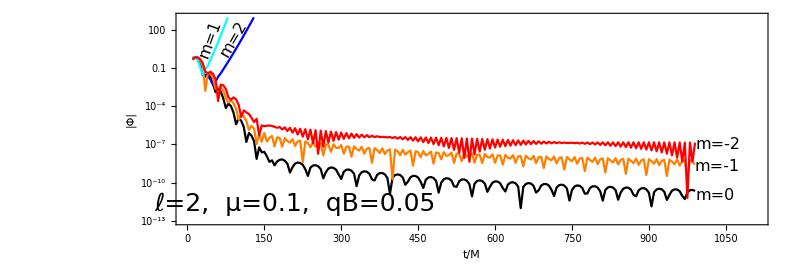

```mathematica
P1000=ListLogPlot[{Abs[DATA1],Abs[DATA2],Abs[DATA3],Abs[DATA4],Abs[DATA5]},Joined->True,FrameStyle->Black,Frame->True,PlotRange->{{0,1110},{10^-13,1000}},BaseStyle->{20,FontFamily->"Times"},PlotStyle->{Black,Blue,Orange,Cyan,Red},FrameLabel->{"t/M","|Φ|"},Epilog->{Text[Style["m=0",FontSize->16],{1030,Log[10^-11]},Background->White],Text[Style["m=-1",FontSize->16],{1033,Log[2 10^-9]},Background->White],Text[Style["m=-2",FontSize->16],{1035,Log[10^-7]}],Text[Rotate[Style["m=1",FontSize->16],70Degree],{45,Log[20]}],Text[Rotate[Style["m=2",FontSize->16],60Degree],{90,Log[20]}],Text[Style["ℓ=2,  μ=0.1,  qB=0.05",FontSize->25],{210,Log[2 10^-12]},Background->White]},ImageSize->800,AspectRatio->1/3]
```

```mathematica
Export["Bobur/QNM_ScalarField/TeX/PLB/TemporalEvol1000.pdf",P1000]
```

Bobur/QNM_ScalarField/TeX/PLB/TemporalEvol1000.pdf

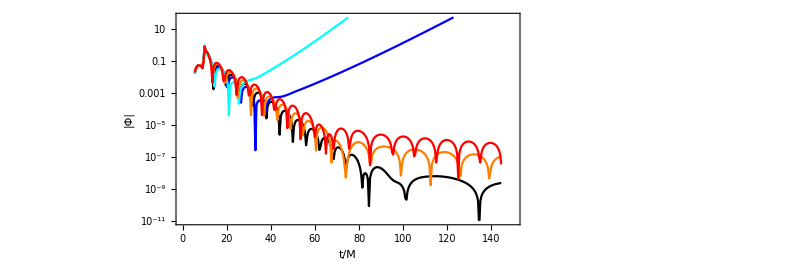

```mathematica
P150=ListLogPlot[{Abs[D1],Abs[D2],Abs[D4],Abs[D3],Abs[D5]},Joined->True,FrameStyle->Black,Frame->True,PlotRange->{{0,150},{10^-11,50}},BaseStyle->{20,FontFamily->"Times"},PlotStyle->{Black,Blue,Cyan,Orange,Red},FrameLabel->{"t/M","|Φ|"},Epilog->{Text[Style["m=0",FontSize->16],{1040,Log[10^-11]},Background->White],Text[Style["m=-1",FontSize->16],{1050,Log[2 10^-10]},Background->White],Text[Style["m=-2",FontSize->16],{1050,Log[2 10^-9]}],Text[Style["m=1"],{200,Log[10^-2]}],Text[Style["m=2"],{180,Log[4]}],Text[Style["ℓ=2",FontSize->25],{200,Log[10^-7]},Background->White]},ImageSize->800,AspectRatio->1/3]
```

```mathematica
Export["Bobur/QNM_ScalarField/TeX/PLB/TemporalEvol150.pdf",P150]
```

Bobur/QNM_ScalarField/TeX/PLB/TemporalEvol150.pdf